## Setup

```mathematica
SetDirectory@NotebookDirectory[]
<<"MagnetCode`"
<<"MathPSfrag`"
Needs["CustomTicks`"]
Needs["ColorbarPlot`"]
```

/Users/will/magcode/examples

```mathematica
mm:=0.001
tesla:=1
ohms:=1
amps:=1
```

### Params

```mathematica
magnet={
MagnetRadius->5mm,
MagnetLength->10mm,
Magnetisation->1 tesla
}
coil={
CoilRadius->7mm,
CoilLength->20mm,
Current->1 amps,
WireRadius->0.1mm,
WireCoating->0.01mm,
CoilResistance->8ohms
}
CalculateCoilParams[parameters__] := 
  ReleaseHold[{
               Hold@Symbol["CoilRadius"]->CoilRadius,
               Hold@Symbol["CoilThickness"]->CoilThickness,
               Hold@Symbol["CoilTurns"]->TotalTurns,
               Hold@Symbol["CoilLength"]->CoilLength,
               Hold@Symbol["Current"]->Current
              } //. 
  Flatten@{{
    CoilThickness -> ( 2 WireLength (WireRadius+WireCoating)^2 ) /
                                (  π CoilLength (CoilRadius+WireRadius+WireCoating) ) ,
    WireLength -> CoilResistance WireArea / WireResistivity ,
    WireResistivity -> 1.7*10^-8, (* copper *)
    WireArea -> π (WireRadius+WireCoating)^2,
    TotalTurns -> TurnsZ TurnsR,
    TurnsZ -> Round[CoilLength / (2WireRadius+2WireCoating)],
    TurnsR -> Round[CoilThickness / (2WireRadius+2WireCoating)]
    },parameters}//.{cm->0.01,mm->0.001,volts->1,ohms->1}]

CalculateCoilParams[coil]
```

## Coil coil filament forces

These equations calculate the forces between two circular coils. The first for coaxial loops, the second including eccentricity. Want to ensure the latter converges to the former for eccentricity converging to zero.

```mathematica
With[{I=1,r=5mm,R=6mm,z=5mm,e=0.1mm},
{Timing@CoilCoilForce[I,I,r,R,z],Timing@CoilCoilForce[I,I,r,R,z,e]}
]
```

{{0.000115,-7.99888×10^-7},{0.047306,{-7.99631×10^-7,-1.30794×10^-8}}}

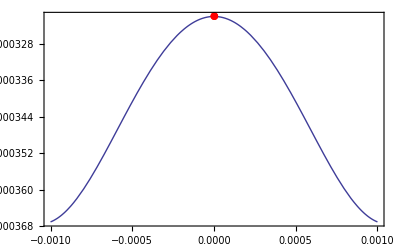

```mathematica
With[{I=1,r=5mm,R=6mm,z=1mm},
Show@{Plot[First@CoilCoilForce[I,I,r,R,z,e],{e,-1mm,1mm},Frame->True],ListPlot[{{0,CoilCoilForce[I,I,r,R,z]}},PlotStyle->Red,PlotMarkers->{Automatic,10}]}
]
```

## Comparison between different methods

Here we hope that a zero-thickness coil and a thin-thickness coil gives similar results.
Eccentricity should result in only small changes in force.

```mathematica
thinvthickparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilLength->20mm,
CoilTurns->100,
Current->1,

Displacement->10mm,
IntegrationPrecision->3,
Verbose->True
};
```

```mathematica
Timing@MagnetCoilForce@{thinvthickparams}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.2mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
Method->"Babic",
CoilThickness->0.2mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.2mm,
Eccentricity->0.1mm
}
```

Coaxial thin coil:

{0.000709,-0.650321}

Coaxial thick coil (plain integral):

{0.018129,-0.642766}

Coaxial thick coil (Babic):

{0.041398,-0.64276}

Eccentric thick coil:

{0.032069,-0.642951}

```mathematica
thickfilamentparams:={

Displacement->10mm,
Eccentricity->0mm,

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->100,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1,

Verbose->True

}
```

```mathematica
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,Method->"Filament",thickfilamentparams}
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,thickfilamentparams}//.thickfilamentparams
```

Coaxial thin coil: (filament)

{0.616156,-0.641207}

Coaxial thin coil:

{0.000661,-0.650321}

```mathematica
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Filament"}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Shell"}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->Automatic}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Babic"}//.thickfilamentparams
```

Coaxial thick coil (filament):

{1.54126,-0.473645}

Coaxial thick coil (shell):

{0.001618,-0.497669}

Coaxial thick coil (plain integral):

{0.012567,-0.49944}

Coaxial thick coil (Babic):

{0.041353,-0.493784}

```mathematica
Timing@MagnetCoilForce@Flatten@{Eccentricity->0.5mm,thickfilamentparams,Method->"Filament"}//.thickfilamentparams
```

{445.86,{-0.474365,0.00284261}}

```mathematica
Timing@MagnetCoilForce@Flatten@{Eccentricity->0.5mm,thickfilamentparams,Method->Automatic}//.thickfilamentparams
```

Eccentric thick coil:

{0.029164,-0.49971}

## Thick coil speed tests

```mathematica
babicparams:={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilThickness->1mm,
CoilLength->20mm,
CoilTurnsR->10,
CoilTurnsZ->40,
Current->1,

Displacement->10mm
}
```

```mathematica
Timing@MagnetCoilForce@{
babicparams,
Method->"Babic",
Verbose->True,
IntegrationPrecision->3
}
Timing@MagnetCoilForce@{
babicparams,
Method->Automatic,
Verbose->True,
IntegrationPrecision->3
}
Timing@MagnetCoilForce@{
babicparams,
Method->"Shell",
Verbose->True,
IntegrationPrecision->3
}
```

Coaxial thick coil (Babic):

{0.04103,-2.45444}

Coaxial thick coil (plain integral):

{0.014643,-2.45486}

Coaxial thick coil (shell):

{0.002832,-2.45475}

```mathematica
babicAccuracy = Table[
Flatten@{
Timing@MagnetCoilForce@{
babicparams,
Method->"Babic",
IntegrationPrecision->ii
},
Timing@MagnetCoilForce@{
babicparams,
IntegrationPrecision->ii
},
Timing@MagnetCoilForce@{
babicparams,
Method->"Shell",
IntegrationPrecision->ii
}}
,{ii,1,8}]
```

{{0.039288,-2.45444,0.011756,-2.4744,0.002588,-2.45475},{0.037703,-2.45444,0.01356,-2.45486,0.002605,-2.45475},{0.037507,-2.45444,0.01338,-2.45486,0.002628,-2.45475},{0.037878,-2.45444,0.020196,-2.45444,0.002609,-2.45475},{0.037814,-2.45444,0.023744,-2.45444,0.002636,-2.45475},{0.038739,-2.45444,0.035562,-2.45444,0.002631,-2.45475},{0.039912,-2.45444,0.058175,-2.45444,0.002668,-2.45475},{0.041301,-2.45444,0.141908,-2.45444,0.002816,-2.45475}}

```mathematica
TableForm[Map[InputForm,babicAccuracy,{2}]]
```

0.0392879999999991 | -2.4544407879895993 | 0.011755999999998323 | -2.4744006907978187 | 0.0025880000000100267 | -2.454751529717687
0.037703000000000486 | -2.4544407879895993 | 0.013560000000005346 | -2.4548594892044457 | 0.002605000000002633 | -2.454751529717687
0.03750699999999796 | -2.4544407879895993 | 0.013380000000005055 | -2.4548594892044457 | 0.002628000000001407 | -2.454751529717687
0.03787799999999919 | -2.4544438306124783 | 0.020196000000005654 | -2.4544392729491915 | 0.002609000000006745 | -2.454751529717687
0.037814000000004455 | -2.4544438306124783 | 0.023744000000000653 | -2.454441045827852 | 0.00263599999999542 | -2.454751529717687
0.03873899999999253 | -2.4544438296675 | 0.03556199999999876 | -2.454443786446628 | 0.002631000000000938 | -2.454751529717687
0.03991200000000106 | -2.454443830093919 | 0.05817499999999853 | -2.4544438175568843 | 0.002668000000006998 | -2.454751529717687
0.04130100000000425 | -2.4544438300903315 | 0.14190800000000792 | -2.4544438299997147 | 0.0028160000000028163 | -2.454751529717687

```mathematica
100(2.454751529717687-2.4544438300903315)/2.4544438300903315
```

0.0125364

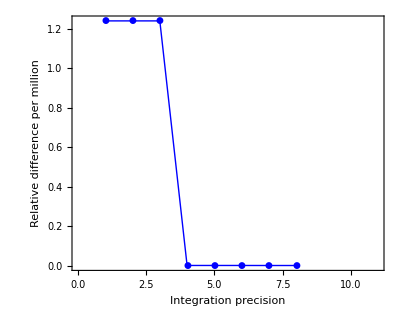
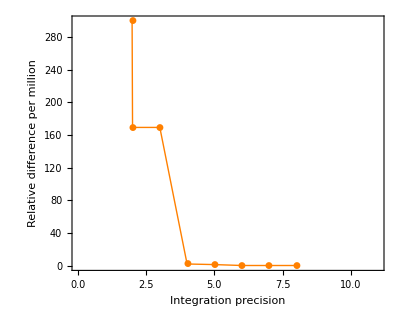

```mathematica
{ListPlot[1000000Abs@{1-babicAccuracy[[All,2]]/babicAccuracy[[-1,2]]},AspectRatio->0.8,PlotStyle->{Blue},PlotRange->{{0,11},Automatic},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}],
ListPlot[1000000Abs@{1-babicAccuracy[[All,4]]/babicAccuracy[[-1,4]]},AspectRatio->0.8,PlotStyle->{Orange},PlotRange->{{0,11},{Automatic,300}},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}]}
```

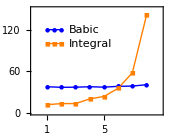

```mathematica
lx:={1,1.5,2,2.5}
ly={120,100};
prectiming=Show@{
ListPlot[1000{babicAccuracy[[All,1]],babicAccuracy[[All,3]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic,6},Joined->True,PlotRange->{{0,9},{0,150}},Frame->True,FrameTicks->{Range[1,8],Automatic,None,None},Axes->False,AspectRatio->0.8,ImageSize->6 72/2.54,FrameLabel->{"Integration precision","Time, ms"}],
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange},Joined->True],
Graphics@Text["Babic",{lx[[4]],ly[[1]]},{-1,0}],
Graphics@Text["Integral",{lx[[4]],ly[[2]]},{-1,0}]
}
```

```mathematica
PSfragExport["fig/prec-timing",prectiming,RenumberTags->True]
```

{fig/prec-timing,fig/prec-timing-psfrag.eps,fig/prec-timing-psfrag.tex}

## Thin coil comparison

```mathematica
filamentparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,

CoilTurns->40,
Current->1

};
```

Single value test:

```mathematica
MagnetCoilForce@Flatten@{Displacement->10mm,Method->"Filament",filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,CoilThickness->0.5mm,filamentparams}//.filamentparams
```

-0.25097

-0.260128

-0.252666

```mathematica
xmax:=40mm
dx:=1mm
Dx:=2dx
thinthin1=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,Method->"Filament",filamentparams}},{x,dx,xmax,Dx}]
thinthin2=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,filamentparams}},{x,0,xmax,dx}]
thinthin3=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->0.5mm,filamentparams}//.thickfilamentparams},{x,2dx,xmax,Dx}]
(* thinthin4=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->1mm,filamentparams}//.thickfilamentparams},{x,3dx,xmax,Dx}] *)
```

{{1.,-0.0230688},{3.,-0.0745112},{5.,-0.144796},{7.,-0.211987},{9.,-0.244502},{11.,-0.251677},{13.,-0.235012},{15.,-0.187111},{17.,-0.123961},{19.,-0.085019},{21.,-0.0606143},{23.,-0.0443491},{25.,-0.033105},{27.,-0.0251338},{29.,-0.0193703},{31.,-0.0151328},{33.,-0.0119703},{35.,-0.0095778},{37.,-0.00774488},{39.,-0.00632412}}

{{0.,0},{1.,-0.024708},{2.,-0.0508108},{3.,-0.0799722},{4.,-0.114387},{5.,-0.155294},{6.,-0.194357},{7.,-0.223162},{8.,-0.242694},{9.,-0.254697},{10.,-0.260128},{11.,-0.259319},{12.,-0.25205},{13.,-0.237481},{14.,-0.213997},{15.,-0.180753},{16.,-0.146335},{17.,-0.119279},{18.,-0.0985976},{19.,-0.0824164},{20.,-0.0694943},{21.,-0.0590167},{22.,-0.0504232},{23.,-0.0433111},{24.,-0.0373815},{25.,-0.0324067},{26.,-0.0282101},{27.,-0.0246524},{28.,-0.0216227},{29.,-0.019032},{30.,-0.0168077},{31.,-0.014891},{32.,-0.0132334},{33.,-0.011795},{34.,-0.0105427},{35.,-0.00944903},{36.,-0.0084909},{37.,-0.00764908},{38.,-0.00690735},{39.,-0.00625201},{40.,-0.00567148}}

{{2.,-0.0510826},{4.,-0.113572},{6.,-0.18813},{8.,-0.235222},{10.,-0.252666},{12.,-0.244858},{14.,-0.208353},{16.,-0.146395},{18.,-0.100073},{20.,-0.0709809},{22.,-0.0517183},{24.,-0.038466},{26.,-0.0291052},{28.,-0.0223582},{30.,-0.0174118},{32.,-0.0137309},{34.,-0.0109539},{36.,-0.00883235},{38.,-0.00719235},{40.,-0.00591064}}

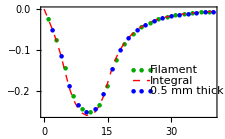

```mathematica
LinSpace[x_,y_,n_]:=Range[x,y,(y-x)/n]
lx:=21+{0,2,4}
ly=LinSpace[-0.15,-0.25,4];
styles={Darker[Green],{Dashed, Red},Blue,Orange};
joined={False,True,False};
markers={{Automatic,6},None,{Automatic,6}};

compareThinPlot=Show[{
ListPlot[{thinthin1},PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧],
ListPlot[{thinthin2},PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[{thinthin3},PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[{thinthin4},PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}}}
,PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧],
ListPlot[
{{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[
{{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}}
,PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[
{{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}}
,PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" 0.5 mm thick",{lx[[3]],ly[[3]]},{-1,0}]
(*Graphics@Text[" 1 mm thick",{lx[[3]],ly[[4]]},{-1,0}]*)
},
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"},
PlotRange->All]
```

```mathematica
PSfragExport["fig/thin-compare",compareThinPlot];
```

## Thick coil comparison

```mathematica
thickfilamentparams:={

Displacement->10mm,
Eccentricity->0mm,

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->100,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1

}
```

```mathematica
thickfilamentparams
xmax:=40mm
dx:=1.5mm
Dx:=2dx
thinthick1=Table[{1000x,MagnetCoilForce[Flatten@{Method->"Filament",Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,0dx,xmax,dx}]
thinthick2=Table[{1000x,MagnetCoilForce[Flatten@{Method->"Shell",Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,1dx,xmax,Dx}]
thinthick3=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Method->Automatic,IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,2dx,xmax,Dx}]
thinthick4=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Method->"Babic",IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,0,xmax,dx}]
```

{Displacement→0.01,Eccentricity→0.,MagnetRadius→0.009,MagnetLength→0.01,Magnetisation→1,CoilRadius→0.01,CoilLength→0.02,CoilThickness→0.005,CoilTurns→100,CoilTurnsR→5,CoilTurnsZ→20,Current→1}

{{0.,0},{1.5,-0.0761861},{3.,-0.156069},{4.5,-0.243116},{6.,-0.3348},{7.5,-0.408819},{9.,-0.456298},{10.5,-0.478114},{12.,-0.475077},{13.5,-0.447058},{15.,-0.394123},{16.5,-0.32498},{18.,-0.26358},{19.5,-0.213897},{21.,-0.174231},{22.5,-0.142632},{24.,-0.117407},{25.5,-0.0971951},{27.,-0.0809227},{28.5,-0.0677554},{30.,-0.0570446},{31.5,-0.0482853},{33.,-0.0410839},{34.5,-0.0351321},{36.,-0.0301876},{37.5,-0.0260592},{39.,-0.0225952}}

{{1.5,-0.0865854},{4.5,-0.27504},{7.5,-0.441957},{10.5,-0.499736},{13.5,-0.449461},{16.5,-0.314449},{19.5,-0.206902},{22.5,-0.138305},{25.5,-0.0945124},{28.5,-0.0660665},{31.5,-0.0472019},{34.5,-0.0344233},{37.5,-0.0255863}}

{{3.,-0.178854},{6.,-0.367523},{9.,-0.480651},{12.,-0.480759},{15.,-0.384914},{18.,-0.25727},{21.,-0.170246},{24.,-0.114832},{27.,-0.0792315},{30.,-0.0559155},{33.,-0.040316},{36.,-0.0296551},{39.,-0.0222187}}

{{0.,0},{1.5,-0.0875787},{3.,-0.178845},{4.5,-0.275189},{6.,-0.367508},{7.5,-0.437844},{9.,-0.480584},{10.5,-0.495865},{12.,-0.484194},{13.5,-0.446026},{15.,-0.384878},{16.5,-0.316759},{18.,-0.257311},{19.5,-0.208938},{21.,-0.17026},{22.5,-0.139438},{24.,-0.114831},{25.5,-0.095111},{27.,-0.0792305},{28.5,-0.0663759},{30.,-0.0559149},{31.5,-0.047356},{33.,-0.0403157},{34.5,-0.034494},{36.,-0.0296549},{37.5,-0.0256124},{39.,-0.0222186}}

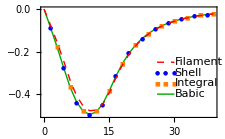

```mathematica
lx:={26,28,30}
ly=Table[i,{i,-0.25,-0.4,-0.05}];
comparePlot=Show@{
ListPlot[{thinthick4},Joined->True,PlotStyle->{Darker[Green]},
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"}],
ListPlot[{thinthick2,thinthick3},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
ListPlot[{thinthick1},Joined->True,PlotStyle->{Dashed,Red}],
ListPlot[{
{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},
{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}
},Joined->True,PlotStyle->{{Dashed,Red},{Dashing[1],Darker[Green]}}],
ListPlot[{
{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}},
{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}
},PlotMarkers->{Automatic,6},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Shell",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[3]]},{-1,0}],
Graphics@Text[" Babic",{lx[[3]],ly[[4]]},{-1,0}]}
```

```mathematica
PSfragExport["fig/thickthin-compare",comparePlot];
```

## Eccentric displacement

```mathematica
eccparam:={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->11.5mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurnsR->5,
CoilTurnsZ->20,
Current->1,

IntegrationPrecision->4

}
```

```mathematica
Timing@MagnetCoilForce@Flatten@{param,
Method->"Filament",
Verbose->True,
RadialForce->False,
Displacement->2mm,
Eccentricity->2mm}
```

Eccentric thick coil: (filament)

$Aborted

```mathematica
Timing@MagnetCoilForce@Flatten@{param,
Verbose->True,
RadialForce->False,
Displacement->2mm,
Eccentricity->2mm}
```

Eccentric thick coil:

{0.028524,-0.111626}

### Integral method without and with eccentricity

Lone point should lie atop the curve

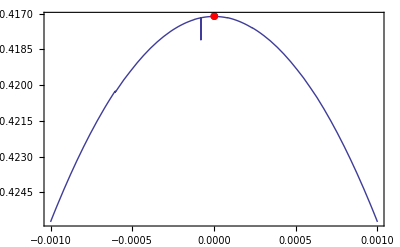

```mathematica
Show[
Plot[MagnetCoilForce@Flatten[{param,Displacement->10mm,Eccentricity->e}],{e,-1mm,1mm},Frame->True,Axes->False],ListPlot[{{0,MagnetCoilForce@Flatten[{param,Displacement->10mm}]}},PlotStyle->Red,PlotMarkers->{Automatic,10}],PlotRange->All]
```

### Constant eccentricity vs filament method

This takes AGES to execute: (quite a number of minutes per point)

```mathematica
h1=Plot[MagnetCoilForce@Flatten@{Method->"Filament",RadialForce->False,param,Displacement->x,Eccentricity->1.5mm},{x,0mm,30mm},PlotStyle->{Red,Dashed},MaxRecursion->1,PlotPoints->10]
```

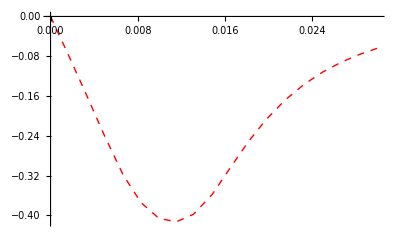

But this one isn’t so bad:

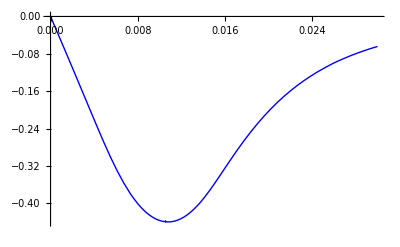

```mathematica
h2=Plot[MagnetCoilForce@Flatten@{RadialForce->False,param,Displacement->x,Eccentricity->1.5mm},{x,0mm,30mm},PlotStyle->{Blue}]
```

Results are pasted inline to avoid having to recalculate them:

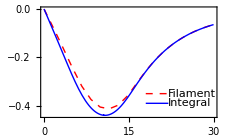

```mathematica
lx:={18,20,22}/1000
ly=-0.35-{0,0.04};
compareEcc=Show[{-Graphics-,-Graphics-,
ListPlot[{
{{lx⟦1⟧,ly⟦1⟧},{lx⟦2⟧,ly⟦1⟧},{lx⟦3⟧,ly⟦1⟧}},
{{lx⟦1⟧,ly⟦2⟧},{lx⟦2⟧,ly⟦2⟧},{lx⟦3⟧,ly⟦2⟧}}
},Joined->True,PlotStyle->{{Dashed,Red},{Dashing[1],Blue}}],
Graphics@Text[" Filament",{lx⟦3⟧,ly⟦1⟧},{-1,0}],
Graphics@Text[" Integral",{lx⟦3⟧,ly⟦2⟧},{-1,0}]
},PlotRange->All,Frame->True,FrameLabel->{"Displacement, mm","Force, N"},FrameTicks->{Table[{ii/1000,ii},{ii,0,30,5}],Automatic,None,None},ImageSize->8 72/2.54]
```

```mathematica
PSfragExport["fig/ecc-compare",compareEcc];
```

### Axial force while varying eccentricity

```mathematica
eccparam
xrange=Flatten@{Range[0,4.5mm,1.5mm],Range[5mm,15mm,0.5mm],Range[16.5mm,30mm,1.5mm]}
```

{MagnetRadius→0.009,MagnetLength→0.01,Magnetisation→1,CoilRadius→0.0115,CoilLength→0.02,CoilThickness→0.005,CoilTurnsR→5,CoilTurnsZ→20,Current→1,IntegrationPrecision→4}

{0.,0.0015,0.003,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0165,0.018,0.0195,0.021,0.0225,0.024,0.0255,0.027,0.0285,0.03}

```mathematica
ecc1=Table[{1000x,MagnetCoilForce@Flatten@{RadialForce->False,eccparam,Displacement->x,Eccentricity->0mm }},{x,xrange}]
```

{{0.,0},{1.5,-0.0798288},{3.,-0.160061},{4.5,-0.238971},{5.,-0.264104},{5.5,-0.288142},{6.,-0.310786},{6.5,-0.331728},{7.,-0.350724},{7.5,-0.367625},{8.,-0.382271},{8.5,-0.394584},{9.,-0.404483},{9.5,-0.412018},{10.,-0.41712},{10.5,-0.4198},{11.,-0.420108},{11.5,-0.418053},{12.,-0.413276},{12.5,-0.407142},{13.,-0.398518},{13.5,-0.387953},{14.,-0.37565},{14.5,-0.361963},{15.,-0.347138},{16.5,-0.299531},{18.,-0.253163},{19.5,-0.212035},{21.,-0.177089},{22.5,-0.14796},{24.,-0.123913},{25.5,-0.104109},{27.,-0.0877967},{28.5,-0.0743427},{30.,-0.0632167}}

```mathematica
ecc2=Table[{1000x,MagnetCoilForce@Flatten@{RadialForce->False,eccparam,Displacement->x,Eccentricity->1mm }},{x,xrange}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{1.5,-0.0807928},{3.,-0.162297},{4.5,-0.243116},{5.,-0.268978},{5.5,-0.293781},{6.,-0.317097},{6.5,-0.338638},{7.,-0.358126},{7.5,-0.375409},{8.,-0.390358},{8.5,-0.402905},{9.,-0.412993},{9.5,-0.420621},{10.,-0.42574},{10.5,-0.428456},{11.,-0.428689},{11.5,-0.426531},{12.,-0.421997},{12.5,-0.41519},{13.,-0.406212},{13.5,-0.395218},{14.,-0.382401},{14.5,-0.36806},{15.,-0.352547},{16.5,-0.303065},{18.,-0.255496},{19.5,-0.213692},{21.,-0.178347},{22.5,-0.148759},{24.,-0.124747},{25.5,-0.104812},{27.,-0.0884024},{28.5,-0.0748691},{30.,-0.0636774}}

```mathematica
ecc3=Table[{1000x,MagnetCoilForce@Flatten@{RadialForce->False,eccparam,Displacement->x,Eccentricity->1.5mm }},{x,xrange}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{1.5,-0.0819687},{3.,-0.165034},{4.5,-0.248255},{5.,-0.275121},{5.5,-0.300889},{6.,-0.325087},{6.5,-0.347366},{7.,-0.367468},{7.5,-0.38523},{8.,-0.400559},{8.5,-0.413387},{9.,-0.423685},{9.5,-0.431438},{10.,-0.436643},{10.5,-0.43933},{11.,-0.4395},{11.5,-0.437191},{12.,-0.431294},{12.5,-0.425326},{13.,-0.415933},{13.5,-0.404394},{14.,-0.390906},{14.5,-0.375759},{15.,-0.359352},{16.5,-0.307399},{18.,-0.258363},{19.5,-0.215734},{21.,-0.179903},{22.5,-0.150222},{24.,-0.12578},{25.5,-0.10547},{27.,-0.0891537},{28.5,-0.075522},{30.,-0.06425}}

```mathematica
ecc4=Table[{1000x,MagnetCoilForce@Flatten@{RadialForce->False,eccparam,Displacement->x,Eccentricity->2mm }},{x,xrange}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{1.5,-0.0835593},{3.,-0.168742},{4.5,-0.25537},{5.,-0.283734},{5.5,-0.310982},{6.,-0.336466},{6.5,-0.364057},{7.,-0.380731},{7.5,-0.399152},{8.,-0.414991},{8.5,-0.4282},{9.,-0.438771},{9.5,-0.4467},{10.,-0.452},{10.5,-0.454684},{11.,-0.454761},{11.5,-0.45232},{12.,-0.445044},{12.5,-0.439682},{13.,-0.429724},{13.5,-0.417494},{14.,-0.402996},{14.5,-0.386671},{15.,-0.368883},{16.5,-0.313324},{18.,-0.262273},{19.5,-0.218533},{21.,-0.182049},{22.5,-0.151944},{24.,-0.127209},{25.5,-0.106899},{27.,-0.0901984},{28.5,-0.076431},{30.,-0.0650454}}

```mathematica
ecc5=Table[{1000x,MagnetCoilForce@Flatten@{RadialForce->False,eccparam,Displacement->x,Eccentricity->2.5mm }},{x,xrange+0.0001}]
```

{{0.1,-0.00567335},{1.6,-0.0912703},{3.1,-0.179263},{4.6,-0.270415},{5.1,-0.300887},{5.6,-0.329915},{6.1,-0.356618},{6.6,-0.380745},{7.1,-0.402176},{7.6,-0.420854},{8.1,-0.436759},{8.6,-0.449886},{9.1,-0.460235},{9.6,-0.467838},{10.1,-0.472696},{10.6,-0.474835},{11.1,-0.474265},{11.6,-0.471002},{12.1,-0.46507},{12.6,-0.456494},{13.1,-0.445323},{13.6,-0.431625},{14.1,-0.415508},{14.6,-0.397173},{15.1,-0.37704},{16.6,-0.316827},{18.1,-0.263861},{19.6,-0.219322},{21.1,-0.182509},{22.6,-0.152283},{24.1,-0.12752},{25.6,-0.107209},{27.1,-0.0905148},{28.6,-0.0767528},{30.1,-0.0653681}}

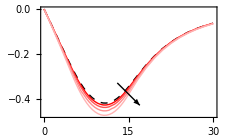

```mathematica
eccPlot=Show[{
ListPlot[ecc1,Joined->True,PlotStyle->{Black,Dashed}],ListPlot[{ecc2,ecc3,ecc4,ecc5},Joined->True,PlotStyle->NestList[Lighter,Red,3]],
Graphics@Arrow[{{13,-0.33},s={17,-0.43}}]},
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"},
ImageSize->8 72/2.54]
```

```mathematica
PSfragExport["fig/ecc-vary",eccPlot]
```

{fig/ecc-vary,fig/ecc-vary-psfrag.eps,fig/ecc-vary-psfrag.tex}

## Radial forces

Todo.

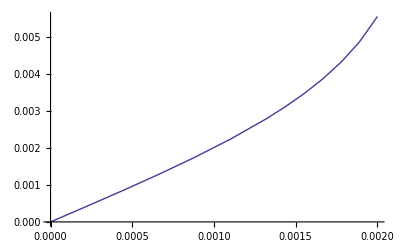

```mathematica
Plot[Last@MagnetCoilForce@Flatten[{Method->"Filament",param,Displacement->0mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```

## Examples

### Outer coil configuration

These are the only fixed variables:

```mathematica
GapRadius:=0.5mm
WireResistivity := 1.7*10^-8 (* copper *)
```

```mathematica
MagVolume:=(20mm)^3
CoilResistance:=4ohms
WireDiam:=1mm
```

```mathematica
WireLength=Nz Sum[2π(rc+dw(n+1/2)),{n,0,Nr-1}]
Assuming[{lc>0},Solve[lw==WireLength//.{Nz->lc/dw,Nr->(Rc-rc)/dw},Rc]//FullSimplify]
```

Nr Nz π (dw Nr+2 rc)

{{Rc→-√((dw^2 lw)/(lc π)+rc^2)},{Rc→√((dw^2 lw)/(lc π)+rc^2)}}

```mathematica
magparam[α_,β_,d_,R_,V_]:=Module[{cr,cR,mr,wa,wl,cl,ct},
mr=(V/(π α))^(1/3); (* magnet radius *)
cr=mr+GapRadius; (* coil radius *)
wa = π (d/2)^2; (* wire area *)
wl=R wa / WireResistivity; (* wire length *)
cl= cr β;(* coil length *)
cR=√((d^2 wl)/(cl π)+cr^2);(* coil outer radius *)
ct=cR-cr; (* coil thickness *)


{Magnetisation->1,Current->-1,MagnetLength->mr α,MagnetRadius->mr,CoilRadius->cr,
CoilLength->cl,CoilThickness->ct,CoilTurnsR->Round[ct/d],CoilTurnsZ->Round[cl/d]} 
]
magparam[α_,β_,d_]:=magparam[α,β,d,CoilResistance,MagVolume]
magparam[α_,β_]:=magparam[α,β,WireDiam,CoilResistance,MagVolume]
magparam[4.75,2.6]
magparam[4.75,2.6,0.5mm]
magparam[4.75,2.6,0.5mm,8ohms,(20mm)^3]
```

{Magnetisation→1,Current→-1,MagnetLength→1.92936 MagVolume^(1/3),MagnetRadius→0.40618 MagVolume^(1/3),CoilRadius→0.0005+0.40618 MagVolume^(1/3),CoilLength→2.6 (0.0005+0.40618 MagVolume^(1/3)),CoilThickness→-0.0005-0.40618 MagVolume^(1/3)+√((0.0005+0.40618 MagVolume^(1/3))^2+(5.65611×10^6 CoilResistance WireDiam^4)/(0.0005+0.40618 MagVolume^(1/3))),CoilTurnsR→Round[(-0.0005-0.40618 MagVolume^(1/3)+√((0.0005+0.40618 MagVolume^(1/3))^2+(5.65611×10^6 CoilResistance WireDiam^4)/(0.0005+0.40618 MagVolume^(1/3))))/WireDiam],CoilTurnsZ→Round[(2.6 (0.0005+0.40618 MagVolume^(1/3)))/WireDiam]}

{Magnetisation→1,Current→-1,MagnetLength→1.92936 MagVolume^(1/3),MagnetRadius→0.40618 MagVolume^(1/3),CoilRadius→0.0005+0.40618 MagVolume^(1/3),CoilLength→2.6 (0.0005+0.40618 MagVolume^(1/3)),CoilThickness→-0.0005+√((3.53507×10^-7 CoilResistance)/(0.0005+0.40618 MagVolume^(1/3))+(0.0005+0.40618 MagVolume^(1/3))^2)-0.40618 MagVolume^(1/3),CoilTurnsR→Round[2000. (-0.0005+√((3.53507×10^-7 CoilResistance)/(0.0005+0.40618 MagVolume^(1/3))+(0.0005+0.40618 MagVolume^(1/3))^2)-0.40618 MagVolume^(1/3))],CoilTurnsZ→Round[5200. (0.0005+0.40618 MagVolume^(1/3))]}

{Magnetisation→1,Current→-1,MagnetLength→0.0385871,MagnetRadius→0.00812361,CoilRadius→0.00862361,CoilLength→0.0224214,CoilThickness→0.0114341,CoilTurnsR→23,CoilTurnsZ→45}

```mathematica
dx:=1mm
xmax:=40mm
```

### Functions I need

```mathematica
MagnetCoilForceFn[x_?NumberQ,a_?NumberQ,b_?NumberQ,d_?NumberQ,R_?NumberQ,V_?NumberQ]:=Module[{s,p},
s=magparam[a,b,d,R,V];
p=Flatten@{Displacement->x,Method->"Shell",s};
MagnetCoilForce[p]
]
MagnetCoilForceFn[x_?NumberQ,a_?NumberQ,b_?NumberQ,d_?NumberQ]:=MagnetCoilForceFn[x,a,b,d,CoilResistance,MagVolume]
MagnetCoilForceFn[x_?NumberQ,a_?NumberQ,b_?NumberQ]:=MagnetCoilForceFn[x,a,b,WireDiam,CoilResistance,MagVolume]
```

```mathematica
DisplMax[α_,β_,d_,R_,V_]:=5Max[{MagnetLength,CoilLength}]//.magparam[α,β,d,R,V]

MagnetCoilForceMax[a_?NumberQ,b_?NumberQ,d_?NumberQ,R_?NumberQ,V_?NumberQ]:=Max@Table[MagnetCoilForceFn[x,a,b,d,R,V],{x,2mm,DisplMax[a,b,d,R,V],DisplMax[a,b,d,R,V]/100}]
MagnetCoilForceMax[a_?NumberQ,b_?NumberQ,d_?NumberQ]:=MagnetCoilForceMax[a,b,d,CoilResistance,MagVolume]
MagnetCoilForceMax[a_?NumberQ,b_?NumberQ]:=MagnetCoilForceMax[a,b,WireDiam,CoilResistance,MagVolume]

MagnetCoilForceMaxAlt[a_?NumberQ,b_?NumberQ,d_?NumberQ,R_?NumberQ,V_?NumberQ]:=FindMaxValue[MagnetCoilForceFn[x,a,b,d,R,V],{x,DisplMax[a,b,d,R,V]/2,1mm,DisplMax[a,b,d,R,V]},AccuracyGoal->2,PrecisionGoal->2]
MagnetCoilForceMaxAlt[a_?NumberQ,b_?NumberQ,d_?NumberQ]:=MagnetCoilForceMaxAlt[a,b,d,CoilResistance,MagVolume]
MagnetCoilForceMaxAlt[a_?NumberQ,b_?NumberQ]:=MagnetCoilForceMaxAlt[a,b,WireDiam,CoilResistance,MagVolume]

MagnetCoilForceMaxScaled[a_?NumberQ,b_?NumberQ,d_?NumberQ,R_?NumberQ,V_?NumberQ]:=CurrentFromDiam[d]×MagnetCoilForceMaxAlt[a,b,d,R,V]
```

Maximum ratio: (only one radial turn; coil thickness = wire diameter)

```mathematica
√((dw^2 lw)/(lc π)+rc^2)-rc==dw
%//.{lw->R aw / ρ,aw -> π (dw/2)^2,rm->(V/(π α))^(1/3),rc->rm+rg,lc->rc β}//FullSimplify
Solve[%,β]
```

-rc+√((dw^2 lw)/(lc π)+rc^2)==dw

√((rg+(V/α)^(1/3)/π^(1/3))^2+(dw^4 π^(1/3) R)/(4 π^(1/3) rg β ρ+4 (V/α)^(1/3) β ρ))==dw+rg+(V/α)^(1/3)/π^(1/3)

```mathematica
β->(dw^3 π^(2/3) R)/(4 (π^(1/3) rg+(V/α)^(1/3)) (π^(1/3) (dw+2 rg)+2 (V/α)^(1/3)) ρ)
```

Minimum ratio (only one axial turn; coil length = wire diameter):

```mathematica
Solve[((V/(π α))^(1/3)+rg) β==d,β]//FullSimplify
```

{{β→(d π^(1/3))/(π^(1/3) rg+(V/α)^(1/3))}}

```mathematica
coilRatioMax[α_,d_,R_,V_]:=(d^3 π^(2/3) R)/(4 (π^(1/3) GapRadius+(V/α)^(1/3)) (π^(1/3) (d+2 GapRadius)+2 (V/α)^(1/3)) WireResistivity)
coilRatioMin[α_,d_,V_]:=d/((V/(π α))^(1/3)+GapRadius)
```

```mathematica
coilRatioMax[0.1,0.2mm,2,0.00022]
coilRatioMin[0.1,0.2mm,0.00022]
```

0.0147357

0.00223958

### Initial results

```mathematica
betarange={0.2,0.5,1,2,4,8};
outercoil1=With[{α=2,MagVolume=(20mm)^3,CoilResistance=4ohms,WireDiam=1mm},
Table[Table[{1000x,MagnetCoilForce@Flatten@{Method->"Shell",Displacement->x,IntegrationPrecision->3,magparam[α,β,WireDiam,CoilResistance,MagVolume]}},{x,0,2xmax,dx}],{β,betarange}]];
```

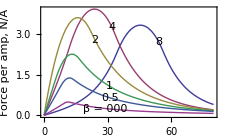

```mathematica
annot[s_]:=PSfrag[s,TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{"<>s<>"}"]
coilratioPlot=Show[{
ListPlot[Reverse@outercoil1,Joined->True,Frame->True,
FrameLabel->{"Displacement, mm","Force per amp, N/A"},
ImageSize->8 72/2.54],
Graphics@Text[PSfrag["β = 000",TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{$\\beta="<>ToString[betarange⟦1⟧]<>"$}"],outercoil1⟦1,30⟧],
Graphics@Text[annot@ToString[betarange⟦2⟧],outercoil1⟦2,32⟧],
Graphics@Text[annot@ToString[betarange⟦3⟧],outercoil1⟦3,32⟧],
Graphics@Text[annot@ToString[betarange⟦4⟧],outercoil1⟦4,25⟧],
Graphics@Text[annot@ToString[betarange⟦5⟧],outercoil1⟦5,33⟧],
Graphics@Text[annot@ToString[betarange⟦6⟧],outercoil1⟦6,55⟧]
}]
```

```mathematica
SetOptions[GuessTag,MaximumTagLength->1];
PSfragExport["fig/magcoil-coilratio",coilratioPlot]
```

{fig/magcoil-coilratio,fig/magcoil-coilratio-psfrag.eps,fig/magcoil-coilratio-psfrag.tex}

```mathematica
alpharange={0.2,0.5,1,2,4};
outercoil2=With[{β=1,MagVolume=(20mm)^3,CoilResistance=4ohms,WireDiam=1mm},
Table[Table[{1000x,MagnetCoilForce@Flatten@{Method->"Shell",Displacement->x,IntegrationPrecision->3,magparam[α,β,WireDiam,CoilResistance,MagVolume]}},{x,0,xmax,dx}],{α,alpharange}]];
```

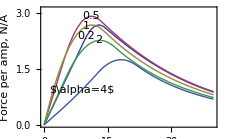

```mathematica
annot[s_]:=PSfrag[s,TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{"<>s<>"}"]
magratioPlot=Show[{
ListPlot[outercoil2,Joined->True],
Graphics@Text[annot@ToString[alpharange⟦1⟧],outercoil2⟦1,11⟧],
Graphics@Text[annot@ToString[alpharange⟦2⟧],outercoil2⟦2,12⟧],
Graphics@Text[annot@ToString[alpharange⟦3⟧],outercoil2⟦3,11⟧],
Graphics@Text[annot@ToString[alpharange⟦4⟧],outercoil2⟦4,14⟧],
Graphics@Text[annot["$\\alpha="<>ToString[alpharange⟦5⟧]<>"$"],outercoil2⟦5,10⟧]
},
Frame->True,
FrameLabel->{None,"Force per amp, N/A"},
ImageSize->8 72/2.54,
PlotRange->{Automatic,{0,3.1}}
]
```

```mathematica
SetOptions[GuessTag,MaximumTagLength->1];
PSfragExport["fig/magcoil-magratio",magratioPlot]
```

{fig/magcoil-magratio,fig/magcoil-magratio-psfrag.eps,fig/magcoil-magratio-psfrag.tex}

#### Initial 2D graph (slow)

```mathematica
ColorbarPlot[MagnetCoilForceMaxAlt[#1,#2]&,{α,0.1,10},{β,0.1,10},XLabel->"Magnet ratio $\\alpha$",YLabel->"Coil ratio $\\beta$",CLabel->"$\\fmax$",Epilog->{PointSize[Medium],Point@{a,b}/.Last@ratiomaxvalue}]
```

-Graphics-

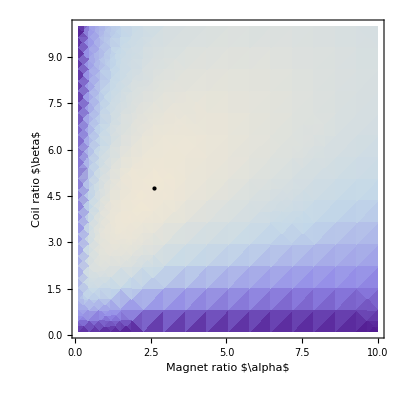
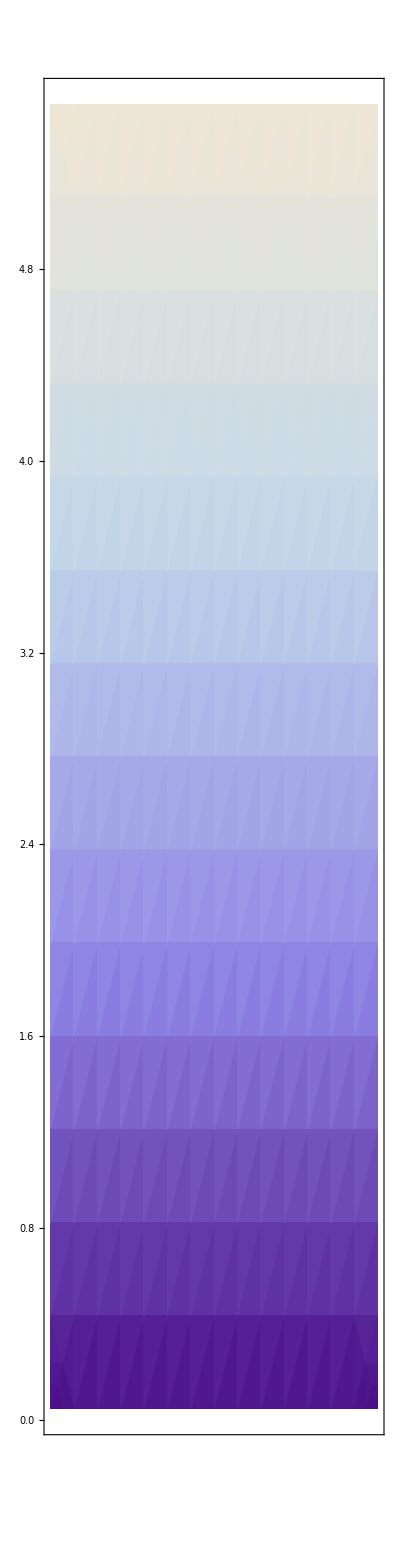
```mathematica
g1=Show[-Graphics-,ImageSize->{Automatic,6 72/2.54},FrameLabel->{PSfrag["Magnet ratio",TeXCommand->"Magnet ratio $\\alpha$"],PSfrag["Coil ratio",TeXCommand->"Coil ratio $\\beta$"],"",""}];
g2=Show[-Graphics-,ImageSize->{Automatic,6 72/2.54},FrameLabel->{" ","",PSfrag["fmax",TeXCommand->"$f_{\\textrm{max}}$, N"],""}];
g3=Row[{g1,g2}]
```

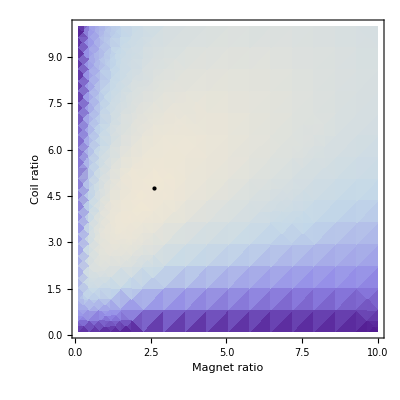
-Graphics--Graphics-

```mathematica
SetOptions[GuessTag,MaximumTagLength->1];
PSfragExport["fig/magcoil-fmax-ratios",g1]
```

{fig/magcoil-fmax-ratios,fig/magcoil-fmax-ratios-psfrag.eps,fig/magcoil-fmax-ratios-psfrag.tex}

```mathematica
PSfragExport["fig/magcoil-fmax-ratios-cbar",g2]
```

{fig/magcoil-fmax-ratios-cbar,fig/magcoil-fmax-ratios-cbar-psfrag.eps,fig/magcoil-fmax-ratios-cbar-psfrag.tex}

### Wire diameter vs peak force

From http://www.powerstream.com/Wire_Size.htm

```mathematica
wireDiam={11.684,10.40384,9.26592,8.25246,7.34822,6.54304,5.82676,5.18922,4.62026,4.1148,3.66522,3.2639,2.90576,2.58826,2.30378,2.05232,1.8288,1.62814,1.45034,1.29032,1.15062,1.02362,0.91186,0.8128,0.7239,0.64516,0.57404,0.51054,0.45466,0.40386,0.36068,0.32004,0.28702,0.254,0.22606,0.2032,0.2,0.18,0.16002,0.14224,0.14,0.127,0.125,0.1143,0.112,0.1016,0.1,0.0889,0.07874}mm;
```

```mathematica
wireCurr={380,328,283,245,211,181,158,135,118,101,89,73,64,55,47,41,35,32,28,22,19,16,14,11,9,7,4.7,3.5,2.7,2.2,1.7,1.4,1.2,0.86,0.7,0.53,0.51,0.43,0.33,0.27,0.26,0.21,0.2,0.17,0.163,0.13,0.126,0.11,0.09};
```

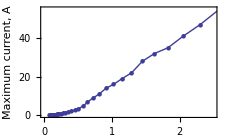

```mathematica
maxcurrPlot=ListPlot[Transpose@{wireDiam/mm,wireCurr},Joined->True,PlotMarkers->{Automatic,6},Frame->True,FrameLabel->{"Wire diameter, mm","Maximum current, A"},ImageSize->8 72/2.54,PlotRange->{{0,2.5},{0,55}}]
```

```mathematica
SetOptions[GuessTag,MaximumTagLength->1];
PSfragExport["fig/magcoil-maxcurr",maxcurrPlot]
```

{fig/magcoil-maxcurr,fig/magcoil-maxcurr-psfrag.eps,fig/magcoil-maxcurr-psfrag.tex}

Verify that the interpolation function is working:

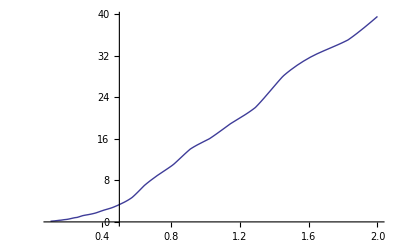

```mathematica
CurrentFromDiam=ListInterpolation[wireCurr,wireDiam];
Plot[CurrentFromDiam[x mm],{x,0.1,2}]
```

### Initial graphs of current from wire diameter

```mathematica
maxcurrratio=Table[
{d,CurrentFromDiam[d]×NMaxValue[{MagnetCoilForceMaxAlt[a,b,d],0.1<b<5&&0.1<a<5},{a,b}]},{d,0.5mm,4.5mm,1mm}]
```

$Aborted

```mathematica
maxcurrratio=Table[
{d,CurrentFromDiam[d]×NMaxValue[{MagnetCoilForceFn[x,a,b,d],1mm<x<50mm,0.1<b<5&&0.1<a<5},{x,b,a}]},{d,0.5mm,5mm,0.25mm}]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaxValue :: cvmit will be suppressed during this calculation.

{{0.0005,18.5423},{0.00075,61.3469},{0.001,85.9584},{0.00125,94.0563},{0.0015,102.471},{0.00175,92.2344},{0.002,85.4526},{0.00225,79.2019},{0.0025,76.0582},{0.00275,72.8941},{0.003,67.9161},{0.00325,64.2278},{0.0035,63.6374},{0.00375,61.9339},{0.004,58.1882},{0.00425,51.9291},{0.0045,54.3208},{0.00475,51.1771},{0.005,50.178}}

```mathematica
maxcurrratio2=Table[
{d,CurrentFromDiam[d]×NMaxValue[{MagnetCoilForceFn[x,a,b,d],1mm<x<50mm,0.1<b<5&&0.1<a<5},{x,b,a}]},{d,0.625mm,4mm,0.25mm}]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaxValue :: cvmit will be suppressed during this calculation.

{{0.000625,39.132},{0.000875,77.1734},{0.001125,92.2789},{0.001375,99.4447},{0.001625,98.3883},{0.001875,87.6789},{0.002125,82.9089},{0.002375,77.9154},{0.002625,73.6516},{0.002875,70.9005},{0.003125,64.832},{0.003375,64.1131},{0.003625,61.1064},{0.003875,58.097}}

```mathematica
maxcurrratio3=Sort[Join[maxcurrratio,maxcurrratio2],#1⟦1⟧<#2⟦1⟧&]
```

{{0.0005,18.5423},{0.000625,39.132},{0.00075,61.3469},{0.000875,77.1734},{0.001,85.9584},{0.001125,92.2789},{0.00125,94.0563},{0.001375,99.4447},{0.0015,102.471},{0.001625,98.3883},{0.00175,92.2344},{0.001875,87.6789},{0.002,85.4526},{0.002125,82.9089},{0.00225,79.2019},{0.002375,77.9154},{0.0025,76.0582},{0.002625,73.6516},{0.00275,72.8941},{0.002875,70.9005},{0.003,67.9161},{0.003125,64.832},{0.00325,64.2278},{0.003375,64.1131},{0.0035,63.6374},{0.003625,61.1064},{0.00375,61.9339},{0.003875,58.097},{0.004,58.1882},{0.00425,51.9291},{0.0045,54.3208},{0.00475,51.1771},{0.005,50.178}}

```mathematica
(* maxcurrratio3[[All,1]]=1000maxcurrratio3[[All,1]] *)
maxcurrratio3
```

{{0.5,18.5423},{0.625,39.132},{0.75,61.3469},{0.875,77.1734},{1.,85.9584},{1.125,92.2789},{1.25,94.0563},{1.375,99.4447},{1.5,102.471},{1.625,98.3883},{1.75,92.2344},{1.875,87.6789},{2.,85.4526},{2.125,82.9089},{2.25,79.2019},{2.375,77.9154},{2.5,76.0582},{2.625,73.6516},{2.75,72.8941},{2.875,70.9005},{3.,67.9161},{3.125,64.832},{3.25,64.2278},{3.375,64.1131},{3.5,63.6374},{3.625,61.1064},{3.75,61.9339},{3.875,58.097},{4.,58.1882},{4.25,51.9291},{4.5,54.3208},{4.75,51.1771},{5.,50.178}}

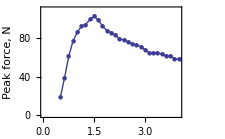

```mathematica
wirediamPlot=ListPlot[maxcurrratio3,Frame->True,Joined->True,PlotMarkers->{Automatic,6},ImageSize->8 72/2.54,FrameLabel->{"Wire diameter, mm","Peak force, N"},PlotRange->{{0,4},{0,110}}]
```

```mathematica
PSfragExport["fig/magcoil-wirediam",wirediamPlot]
```

{fig/magcoil-wirediam,fig/magcoil-wirediam-psfrag.eps,fig/magcoil-wirediam-psfrag.tex}

### Trying to improve the efficiency

```mathematica
Timing[FindMaximum[{MagnetCoilForceFn[x,a,b,1mm],0.1mm<x,0.01<b&&0.01<a},{x,b,a}]]
```

{13.7739,{55.4536,{x→0.0202272,b→1.7197,a→0.226711}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceFn[x,a,b,1mm],0.1mm<x,0.01<b&&0.01<a},{x,b,a}]]
```

{150.782,{58.7854,{x→0.0202197,b→1.79212,a→0.260385}}}

```mathematica
Timing[FindMaximum[{MagnetCoilForceFn[x,a,b,1mm],0.1mm<x<100mm,0.01<b&&0.01<a},{x,b,a}]]
```

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.54409×10^-6, 6.24281, 8.2683×10^-7}, is returned.

{178.836,{74.6697,{x→0.0229126,b→2.81315,a→0.736058}}}

```mathematica
Timing[FindMaximum[{MagnetCoilForceFn[x,a,b,1mm],0.1mm<x<100mm,0.01<b<10&&0.01<a<10},{x,b,a}]]
```

FindMaximum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.54183×10^-8, 6.79177, 4.65902×10^-9}, is returned.

{190.512,{77.5827,{x→0.0228081,b→2.85566,a→0.788586}}}

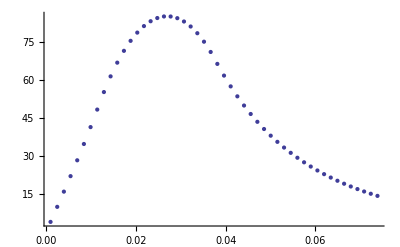

```mathematica
With[{d=1mm,b=4.75,a=2.6},ListPlot[Table[{x,MagnetCoilForceFn[x,a,b,d]},{x,1mm,DisplMax[a,b,d],DisplMax[a,b,d]/50}]]]
```

```mathematica
Timing[MagnetCoilForceMax[a,b,1mm]//.{b->4.75,a->2.6}]
Timing[MagnetCoilForceMaxAlt[a,b,1mm]//.{b->4.75,a->2.6}]
```

{0.597716,85.0427}

{0.186913,85.0557}

```mathematica
Timing[NMaximize[{MagnetCoilForceMax[aa,bb,1mm],0.1<bb<10&&0.1<aa<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2,MaxIterations->10]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 10 iterations.

{38.5567,{85.2824,{aa→1.96784,bb→4.20377}}}

```mathematica
Timing[FindMaximum[MagnetCoilForceMaxAlt[aa,bb,1mm],{aa,3,0.1,10},{bb,3,0.1,10},AccuracyGoal->3,PrecisionGoal->2,MaxIterations->10]]
```

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue :: lstol will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaxValue :: sdprec will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{58.303,{82.1814,{aa→1.37201,bb→4.38101}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceMax[aa,bb,1mm],0.1<bb<10&&0.1<aa<10},{aa,bb}]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{251.575,{86.2697,{aa→2.03541,bb→4.30144}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceMax[aa,bb,1mm],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->4,PrecisionGoal->3]]
```

{68.118,{85.9194,{aa→2.06624,bb→4.32211}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceMax[aa,bb,1mm],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]]
```

{68.6043,{85.9194,{aa→2.06624,bb→4.32211}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceMaxAlt[aa,bb,1mm],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]]
```

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaxValue :: lstol will be suppressed during this calculation.

FindMaxValue::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{45.8392,{86.004,{aa→2.06624,bb→4.32211}}}

```mathematica
Timing[NMaximize[{MagnetCoilForceMax[aa,bb,1mm],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->2,PrecisionGoal->2,MaxIterations->10]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 10 iterations.

{38.7069,{85.2824,{aa→1.96784,bb→4.20377}}}

### This was a big fat waste of time

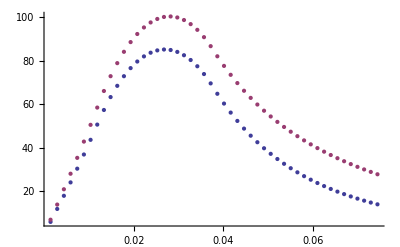

```mathematica
Block[{V,x1,x2,d=1mm,b=4.75,a=2.6,dmax},
V=(20mm)^3;
dmax=DisplMax[a,b,d];
x1=Table[{x,MagnetCoilForceFn[x,a,b,d,4ohms,V]},{x,dmax/50,dmax,dmax/50}];
x2=Table[{x,MagnetCoilForceFn[x,a,b,d,8ohms,V]},{x,dmax/50,dmax,dmax/50}];
ListPlot[{x1,x2}]
]
```

Sorry the code below is ugly.

```mathematica
MagVolume:=(20mm)^3
CoilResistance:=8ohms
Timing[maxrange23=Table[
{d,NMaximize[{MagnetCoilForceMax[aa,bb,d],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]},{d,0.5mm,4mm,0.25mm}]]
CoilResistance:=4ohms
Timing[maxrange22=Table[
{d,NMaximize[{MagnetCoilForceMax[aa,bb,d],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]},{d,0.5mm,4mm,0.25mm}]]
CoilResistance:=2ohms
Timing[maxrange21=Table[
{d,NMaximize[{MagnetCoilForceMax[aa,bb,d],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]},{d,0.5mm,4mm,0.25mm}]]
CoilResistance:=4ohms
MagVolume:=(40mm)^3
Timing[maxrange12=Table[
{d,NMaximize[{MagnetCoilForceMax[aa,bb,d],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]},{d,0.5mm,4mm,0.25mm}]]
MagVolume:=(10mm)^3
Timing[maxrange32=Table[
{d,NMaximize[{MagnetCoilForceMax[aa,bb,d],0.1<aa<10&&0.1<bb<10},{aa,bb},AccuracyGoal->3,PrecisionGoal->2]},{d,0.5mm,4mm,0.25mm}]]
MagVolume:=(20mm)^3
```

{11383.,{{0.0005,{30.3268,{aa→1.88681,bb→1.82851}}},{0.00075,{80.132,{aa→1.85073,bb→3.32617}}},{0.001,{104.686,{aa→2.24187,bb→6.10006}}},{0.00125,{113.421,{aa→2.31937,bb→9.9169}}},{0.0015,{125.984,{aa→1.74931,bb→9.97172}}},{0.00175,{110.073,{aa→0.886787,bb→7.91885}}},{0.002,{107.844,{aa→0.837668,bb→9.99343}}},{0.00225,{101.886,{aa→0.613127,bb→9.99494}}},{0.0025,{96.4479,{aa→0.598837,bb→9.96691}}},{0.00275,{91.922,{aa→0.407976,bb→9.9622}}},{0.003,{86.2142,{aa→0.27417,bb→9.96875}}},{0.00325,{81.5746,{aa→0.356132,bb→9.9529}}},{0.0035,{80.1616,{aa→0.298361,bb→9.95278}}},{0.00375,{77.2299,{aa→0.250525,bb→9.9521}}},{0.004,{73.9321,{aa→0.392027,bb→9.91918}}}}}

{5712.24,{{0.0005,{20.3797,{aa→1.51009,bb→1.12252}}},{0.00075,{60.9185,{aa→2.535,bb→2.61104}}},{0.001,{85.9194,{aa→2.06624,bb→4.32211}}},{0.00125,{96.2498,{aa→2.61358,bb→7.74403}}},{0.0015,{110.746,{aa→2.3246,bb→9.9269}}},{0.00175,{104.054,{aa→2.00799,bb→9.90433}}},{0.002,{101.151,{aa→1.05948,bb→9.43361}}},{0.00225,{95.1991,{aa→0.81506,bb→8.86999}}},{0.0025,{93.2297,{aa→0.845427,bb→9.99343}}},{0.00275,{76.9874,{aa→0.149592,bb→6.57295}}},{0.003,{85.5111,{aa→0.457739,bb→9.97902}}},{0.00325,{80.6645,{aa→0.467247,bb→9.98732}}},{0.0035,{79.5244,{aa→0.314269,bb→9.95186}}},{0.00375,{77.3794,{aa→0.298361,bb→9.95278}}},{0.004,{73.7794,{aa→0.348797,bb→9.95881}}}}}

{3579.54,{{0.0005,{10.8545,{aa→0.437528,bb→0.424509}}},{0.00075,{44.2105,{aa→2.68289,bb→2.29099}}},{0.001,{67.9614,{aa→2.1038,bb→3.27732}}},{0.00125,{78.5039,{aa→2.27964,bb→4.79624}}},{0.0015,{93.2046,{aa→2.20719,bb→6.54024}}},{0.00175,{92.2826,{aa→2.85671,bb→9.62251}}},{0.002,{91.0765,{aa→2.05221,bb→9.57527}}},{0.00225,{89.9939,{aa→1.61724,bb→9.56821}}},{0.0025,{84.9459,{aa→1.10488,bb→8.14693}}},{0.00275,{85.0173,{aa→1.13267,bb→9.41114}}},{0.003,{78.2763,{aa→1.7223,bb→9.71284}}},{0.00325,{79.0345,{aa→0.578702,bb→9.93537}}},{0.0035,{68.1974,{aa→0.142621,bb→6.91042}}},{0.00375,{76.8308,{aa→0.4512,bb→9.95942}}},{0.004,{72.5563,{aa→0.443955,bb→9.98144}}}}}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{3395.08,{{0.0005,{28.5871,{aa→0.220721,bb→0.195252}}},{0.00075,{136.149,{aa→0.507705,bb→0.593778}}},{0.001,{297.748,{aa→1.99857,bb→1.9166}}},{0.00125,{388.426,{aa→2.25972,bb→3.0337}}},{0.0015,{503.2,{aa→2.32717,bb→3.876}}},{0.00175,{518.16,{aa→2.03136,bb→4.96822}}},{0.002,{538.881,{aa→2.84477,bb→7.2423}}},{0.00225,{555.808,{aa→3.12683,bb→9.93879}}},{0.0025,{574.147,{aa→2.73007,bb→9.92427}}},{0.00275,{580.016,{aa→2.09751,bb→9.90433}}},{0.003,{574.05,{aa→1.52669,bb→9.99822}}},{0.00325,{558.196,{aa→1.24442,bb→9.99509}}},{0.0035,{561.363,{aa→1.04742,bb→9.66059}}},{0.00375,{559.482,{aa→1.06581,bb→9.99984}}},{0.004,{537.402,{aa→0.834643,bb→9.99686}}}}}

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

$Aborted

```mathematica
Timing@MagnetCoilForceMaxAlt[1,1,1mm,4ohms,(20mm)^3]
```

{0.384859,44.9394}

### New tables of maximums

```mathematica
Drange=Range[0.2mm,2.5mm,0.1mm];
Rrange={2ohms,4ohms,8ohms};
Vrange={(15mm)^3,(20mm)^3,(25mm)^3};
ND=Length@Drange;
NR=Length@Rrange;
NV=Length@Vrange;
amin=0.1;
amax=10.1;
Nratios=20;
magRatios=Range[amin,amax,(amax-amin)/Nratios];
```

```mathematica
Block[{d=WireDiam,R=CoilResistance,V=MagVolume,a=1,b=1},
bmin=coilRatioMin[a,d,V];
bmax=coilRatioMax[a,d,R,V];
Print[ToString@bmin<>" <-> "<>ToString@bmax];
MagnetCoilForceMaxAlt[a,b,d,R,V]
]
```

0.070643 <-> 141.77

2.68045

```mathematica
Table[
Timing[
ratiodata[dd,rr,vv]=Block[{bmin,bmax,coilRatios},
Table[
bmin=Max[coilRatioMin[a,dd,vv],0.1];
bmax=Min[coilRatioMax[a,dd,rr,vv],10];
coilRatios=Range[bmin,bmax,(bmax-bmin)/Nratios];
Table[{a,b,MagnetCoilForceMaxScaled[a,b,dd,rr,vv]},{b,coilRatios}],{a,magRatios}]
];],{dd,{1mm}},{rr,{4ohms}},{vv,{(20mm)^3}}]
```

{{{{105.002,Null}}}}

```mathematica
datafile="data/Thick-Coil-Magnet-Data.mx";
If[FindFile[datafile]===$Failed,
(* regenerate data *)
Table[
Timing[
ratiodata[dd,rr,vv]=Block[{bmin,bmax,coilRatios},
Table[
bmin=Max[coilRatioMin[a,dd,vv],0.1];
bmax=Min[coilRatioMax[a,dd,rr,vv],10];
coilRatios=Range[bmin,bmax,(bmax-bmin)/Nratios];
Table[{a,b,MagnetCoilForceMaxScaled[a,b,dd,rr,vv]},{b,coilRatios}],{a,magRatios}]
];],{dd,Drange},{rr,Rrange},{vv,Vrange}];
Save[datafile,{ratiodata}];
,
(* load data *)
DumpGet[datafile];
]
```

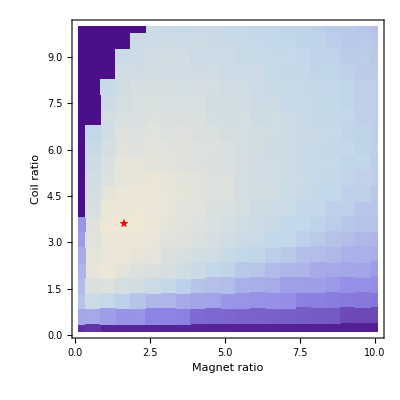
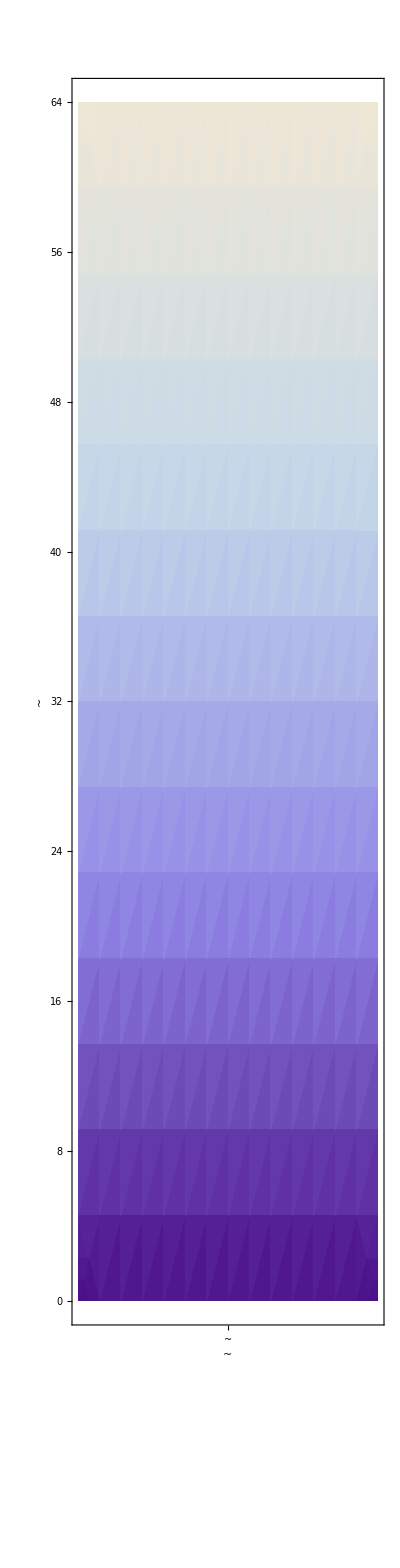

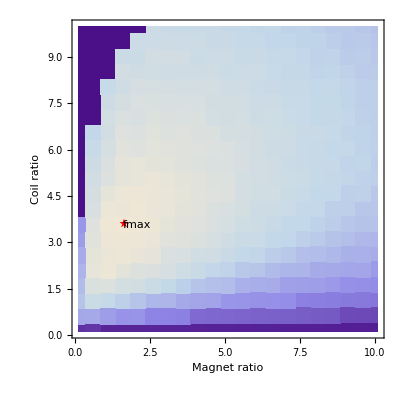
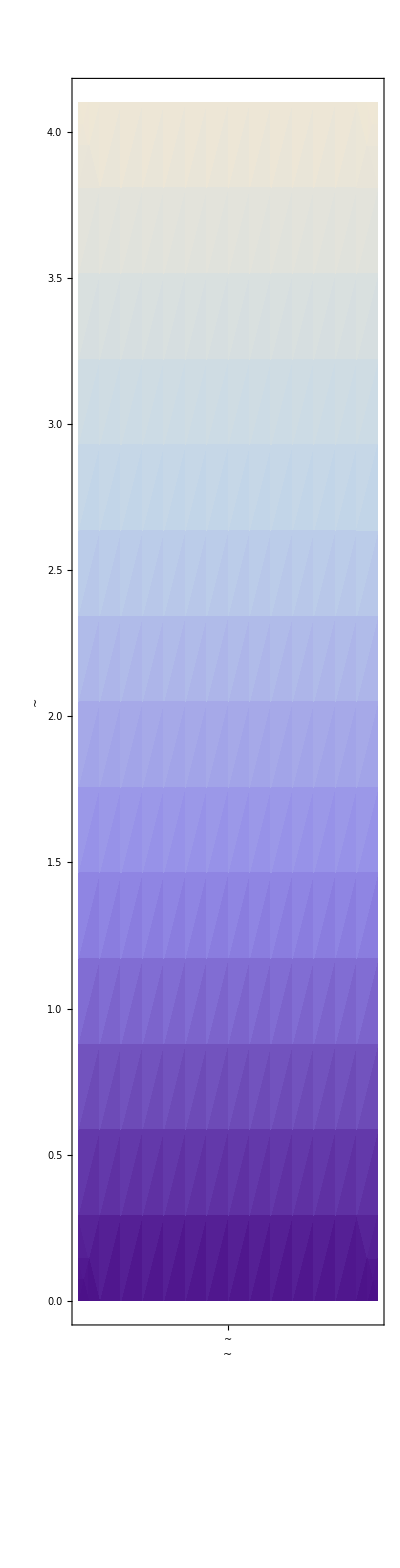

```mathematica
Block[{dd=1mm,rr=4ohms,vv=(20mm)^3},
size=6 72/2.54;
data=Partition[Flatten@ratiodata[dd,rr,vv],3];
max=Max[data⟦All,3⟧];
maxpos=Position[data,max];
g1=Show[
{
ListDensityPlot[data,InterpolationOrder->0],
ListPlot[{data⟦maxpos⟦1,1⟧,{1,2}⟧},PlotMarkers->{★,Medium},PlotStyle->Red]
},
FrameLabel->{PSfrag["Magnet ratio",TeXCommand->"Magnet ratio, $\\ratioMag$"],PSfrag["Coil ratio",TeXCommand->"Coil ratio, $\\ratioCoil$"],"",""},ImageSize->{Automatic,size}];
g2=DensityPlot[y,{x,0,1},{y,0,max},AspectRatio->10,ImageSize->{Automatic,size},FrameTicks->{{{0.5,PSfrag["~",TeXCommand->""]}},Automatic,None,None},FrameLabel->{PSfrag["~",TeXCommand->""],PSfrag["~",TeXCommand->""],PSfrag["fmax",TeXCommand->"$\\fpeak/\\currentCoil$"],PSfrag["~",TeXCommand->""]},PlotRange->{Automatic,{0,max}}];
]
Row[{g1,g2}]

Block[{dd=1mm,rr=4ohms,vv=(20mm)^3},
size=6 72/2.54;
data=#*{1,1,1/CurrentFromDiam[dd]}&/@Partition[Flatten@ratiodata[dd,rr,vv],3];
max=Max[data⟦All,3⟧];
maxpos=Position[data,max];
g1=Show[
{
ListDensityPlot[data,InterpolationOrder->0],
ListPlot[{data⟦maxpos⟦1,1⟧,{1,2}⟧},PlotMarkers->{★,Medium},PlotStyle->Red],
Graphics@Text[PSfrag["fmax",TeXCommand->"$\\fnmax$"],data⟦maxpos⟦1,1⟧,{1,2}⟧,{-2,0}]
},
FrameLabel->{PSfrag["Magnet ratio",TeXCommand->"Magnet ratio, $\\ratioMag$"],PSfrag["Coil ratio",TeXCommand->"Coil ratio, $\\ratioCoil$"],"",""},ImageSize->{Automatic,size}];
g2=DensityPlot[y,{x,0,1},{y,0,max},AspectRatio->10,ImageSize->{Automatic,size},FrameTicks->{{{0.5,PSfrag["~",TeXCommand->""]}},Automatic,None,None},FrameLabel->{PSfrag["~",TeXCommand->""],PSfrag["~",TeXCommand->""],PSfrag["norm fmax",TeXCommand->"$\\fnpeak$"],PSfrag["~",TeXCommand->""]},PlotRange->{Automatic,{0,max}}];
]
Row[{g1,g2}]
```

```mathematica
PSfragExport["fig/magratio-maxforce",g1];
PSfragExport["fig/magratio-maxforce-cb",g2];
```

```mathematica
RatioDataAtMax[dd_,rr_,vv_]:=
Module[{data,max,maxpos},
data=Partition[Flatten@ratiodata[dd,rr,vv],3];
max=Max[Part[Partition[data,3],;;,3]];
maxpos=Position[data,max]⟦1,1⟧;
data⟦maxpos⟧
]
```

```mathematica
With[{dd=1mm,vv=(20mm)^3,rr=4ohms},
RatioDataAtMax[dd,rr,vv]
]
```

{2.1,4.06,63.3218}

### Alternative approach #3

```mathematica
MagnetCoilForceMaxScaledBound[a_,b_,dd_,rr_,vv_]:=Module[{},
If[coilRatioMin[a,dd,vv]<b<coilRatioMax[a,dd,rr,vv],
MagnetCoilForceMaxScaled[a,b,dd,rr,vv],
0
]
]
```

```mathematica
Timing[With[{dd=1mm,rr=4ohms,vv=(20mm)^3},
NMaximize[{MagnetCoilForceMaxScaledBound[a,b,dd,rr,vv],a>0.1,b>0.1},{{a,0.1,10},{b,0.1,10}}]
]]
```

{86.3261,{65.4678,{a→1.20679,b→2.96406}}}

```mathematica
CalcRatioMax[dd_,rr_,vv_]:=Module[{},
If[ValueQ@ratiomax[dd,rr,vv],
(* true *)
Print["Already calculated for d="<>ToString[dd/mm]<>" mm, r="<>ToString[rr ]<>" ohm, v=("<>ToString[(vv)^(1/3)/mm]<>"mm)^3"], 
(* false *)
Print["Calculating for d="<>ToString[dd/mm]<>" mm, r="<>ToString[rr ]<>" ohm, v=("<>ToString[(vv)^(1/3)/mm]<>"mm)^3"];
ratiomax[dd,rr,vv]=NMaximize[
{MagnetCoilForceMaxScaledBound[a,b,dd,rr,vv],a>0.1,b>0.1},
{{a,0.1,10},{b,0.1,10}}
]
]
]
```

```mathematica
Get["data/magratio-max.mx",{ratiomax}];
With[{rr=32ohms,vv=(15mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=32ohms,vv=(20mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=32ohms,vv=(25mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=28ohms,vv=(15mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=28ohms,vv=(20mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=28ohms,vv=(25mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=24ohms,vv=(15mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=24ohms,vv=(20mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
With[{rr=24ohms,vv=(25mm)^3,Drange=Range[5,25,1]/10 mm},
CalcRatioMax[#,rr,vv]&/@Drange
]
Save["data/magratio-max.mx",{ratiomax}]
```

Get::notencode: Warning: The file "data/magratio-max.mx" is not encoded.

Already calculated for d=0.5 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=0.6 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=0.7 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=0.8 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=0.9 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1. mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.1 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.2 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.3 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.4 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.5 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.6 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.7 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.8 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=1.9 mm, r=32 ohm, v=(15.mm)^3

Already calculated for d=2. mm, r=32 ohm, v=(15.mm)^3

Calculating for d=2.1 mm, r=32 ohm, v=(15.mm)^3

Calculating for d=2.2 mm, r=32 ohm, v=(15.mm)^3

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Calculating for d=2.3 mm, r=32 ohm, v=(15.mm)^3

Calculating for d=2.4 mm, r=32 ohm, v=(15.mm)^3

Calculating for d=2.5 mm, r=32 ohm, v=(15.mm)^3

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,{48.898,{a→1.30697,b→21.8142}},{43.2734,{a→0.2477,b→15.068}},{47.2505,{a→1.22821,b→26.3974}},{46.7463,{a→1.23259,b→24.4723}},{46.4399,{a→1.23586,b→25.2645}}}

Calculating for d=0.5 mm, r=32 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.6 mm, r=32 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.7 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=0.8 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=0.9 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1. mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.1 mm, r=32 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=1.2 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.3 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.4 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.5 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.6 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.7 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.8 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=1.9 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2. mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2.1 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2.2 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2.3 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2.4 mm, r=32 ohm, v=(20.mm)^3

Calculating for d=2.5 mm, r=32 ohm, v=(20.mm)^3

{{43.3109,{a→1.82723,b→3.32051}},{63.8696,{a→1.31144,b→3.02875}},{83.8863,{a→1.45407,b→3.15048}},{94.3922,{a→1.46504,b→5.14234}},{105.472,{a→1.86891,b→6.48614}},{106.675,{a→1.47957,b→5.88753}},{107.832,{a→1.84375,b→8.17691}},{108.725,{a→1.46469,b→8.19198}},{109.307,{a→1.46439,b→8.87407}},{115.551,{a→1.59132,b→9.81419}},{118.06,{a→1.49437,b→11.3908}},{115.272,{a→1.67218,b→10.7289}},{111.651,{a→1.49587,b→13.0503}},{105.36,{a→1.5705,b→10.6547}},{105.267,{a→1.23326,b→15.4338}},{104.851,{a→1.6012,b→15.5268}},{86.2721,{a→0.132566,b→7.35113}},{102.294,{a→1.21586,b→14.8108}},{101.462,{a→1.31993,b→19.6272}},{100.536,{a→1.21079,b→18.4793}},{99.9635,{a→1.23561,b→19.1859}}}

Calculating for d=0.5 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=0.6 mm, r=32 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.7 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=0.8 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=0.9 mm, r=32 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=1. mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.1 mm, r=32 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=1.2 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.3 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.4 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.5 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.6 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.7 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.8 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=1.9 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2. mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2.1 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2.2 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2.3 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2.4 mm, r=32 ohm, v=(25.mm)^3

Calculating for d=2.5 mm, r=32 ohm, v=(25.mm)^3

{{62.029,{a→2.14987,b→3.44244}},{99.5555,{a→1.30263,b→3.06888}},{138.627,{a→1.79947,b→3.3117}},{154.762,{a→1.36909,b→3.04929}},{178.539,{a→1.38382,b→4.52338}},{181.973,{a→1.48447,b→4.8178}},{185.845,{a→1.73777,b→6.24917}},{188.323,{a→1.49465,b→6.80517}},{190.397,{a→1.42618,b→7.42756}},{202.162,{a→1.64947,b→8.85132}},{207.656,{a→1.60149,b→9.49319}},{203.874,{a→1.1968,b→9.12084}},{197.495,{a→1.30448,b→9.85903}},{189.595,{a→1.27293,b→9.35983}},{184.841,{a→1.11892,b→9.02781}},{187.793,{a→1.52734,b→12.074}},{182.162,{a→1.36016,b→9.70382}},{184.176,{a→1.37943,b→14.7972}},{182.122,{a→1.30926,b→14.4971}},{181.006,{a→1.33081,b→15.6568}},{177.508,{a→2.22396,b→21.0832}}}

Calculating for d=0.5 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=0.6 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=0.7 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=0.8 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=0.9 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1. mm, r=28 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=1.1 mm, r=28 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=1.2 mm, r=28 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=1.3 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.4 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.5 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.6 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.7 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.8 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=1.9 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2. mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2.1 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2.2 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2.3 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2.4 mm, r=28 ohm, v=(15.mm)^3

Calculating for d=2.5 mm, r=28 ohm, v=(15.mm)^3

{{23.2788,{a→1.4183,b→3.09393}},{31.5102,{a→0.968812,b→2.84779}},{42.6325,{a→1.753,b→5.64263}},{46.4497,{a→1.60607,b→6.53288}},{51.4471,{a→1.63538,b→6.99991}},{51.3623,{a→1.4482,b→8.2178}},{51.482,{a→1.75877,b→10.3453}},{51.4822,{a→1.27737,b→9.71908}},{51.5702,{a→1.42975,b→10.9112}},{54.2377,{a→1.47202,b→12.0063}},{55.1844,{a→1.40099,b→12.1983}},{53.8209,{a→1.21103,b→13.5331}},{51.4468,{a→2.19216,b→17.3365}},{49.6031,{a→1.29524,b→19.1903}},{48.8816,{a→1.27836,b→18.6429}},{48.2605,{a→1.17121,b→21.4365}},{48.1637,{a→1.21669,b→20.7012}},{47.2139,{a→1.22146,b→20.841}},{46.4162,{a→1.78192,b→27.1183}},{46.2333,{a→1.61977,b→27.7199}},{45.7901,{a→1.22364,b→25.6814}}}

Calculating for d=0.5 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=0.6 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=0.7 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=0.8 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=0.9 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1. mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.1 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.2 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.3 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.4 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.5 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.6 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.7 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.8 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=1.9 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2. mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2.1 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2.2 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2.3 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2.4 mm, r=28 ohm, v=(20.mm)^3

Calculating for d=2.5 mm, r=28 ohm, v=(20.mm)^3

{{41.1029,{a→1.80811,b→3.26668}},{61.4243,{a→1.3157,b→3.03189}},{81.435,{a→1.51246,b→3.13395}},{90.6699,{a→1.54992,b→3.86997}},{102.462,{a→1.29763,b→5.63374}},{103.968,{a→1.31439,b→5.74565}},{105.442,{a→1.78272,b→7.24786}},{106.055,{a→1.38308,b→7.00823}},{106.883,{a→1.40186,b→8.85331}},{113.192,{a→1.39615,b→9.19164}},{115.641,{a→1.73242,b→10.299}},{113.61,{a→1.57054,b→10.9079}},{109.295,{a→1.63115,b→13.1357}},{102.33,{a→1.4902,b→9.32123}},{99.2798,{a→1.6093,b→9.45864}},{103.317,{a→1.29658,b→16.0484}},{101.489,{a→2.33663,b→19.5583}},{83.9596,{a→0.142502,b→6.89459}},{99.3373,{a→1.12187,b→18.2926}},{98.8158,{a→1.20386,b→18.0854}},{98.4742,{a→1.19477,b→18.9802}}}

Calculating for d=0.5 mm, r=28 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.6 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=0.7 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=0.8 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=0.9 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1. mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.1 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.2 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.3 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.4 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.5 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.6 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.7 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.8 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=1.9 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=2. mm, r=28 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=2.1 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=2.2 mm, r=28 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=2.3 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=2.4 mm, r=28 ohm, v=(25.mm)^3

Calculating for d=2.5 mm, r=28 ohm, v=(25.mm)^3

{{60.5165,{a→1.63179,b→1.42983}},{95.033,{a→1.77815,b→3.26944}},{132.737,{a→1.4296,b→3.14007}},{150.33,{a→1.34928,b→3.03497}},{167.645,{a→1.08762,b→3.02661}},{176.816,{a→1.50689,b→4.71119}},{179.575,{a→1.09604,b→4.99832}},{183.429,{a→1.72038,b→6.30695}},{185.81,{a→1.61958,b→7.56555}},{197.844,{a→1.59884,b→7.65011}},{203.349,{a→1.57017,b→8.64274}},{200.112,{a→1.68043,b→9.0997}},{193.165,{a→1.27356,b→8.73662}},{186.803,{a→1.31891,b→10.2521}},{184.444,{a→1.36142,b→10.694}},{184.077,{a→1.21485,b→10.9714}},{182.831,{a→1.15233,b→11.45}},{179.642,{a→1.64845,b→11.8462}},{179.055,{a→1.45951,b→14.2854}},{177.958,{a→1.55246,b→16.2973}},{175.787,{a→2.06123,b→18.0591}}}

Calculating for d=0.5 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=0.6 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=0.7 mm, r=24 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.8 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=0.9 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1. mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.1 mm, r=24 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=1.2 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.3 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.4 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.5 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.6 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.7 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.8 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=1.9 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=2. mm, r=24 ohm, v=(15.mm)^3

Calculating for d=2.1 mm, r=24 ohm, v=(15.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=2.2 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=2.3 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=2.4 mm, r=24 ohm, v=(15.mm)^3

Calculating for d=2.5 mm, r=24 ohm, v=(15.mm)^3

{{22.3349,{a→1.62171,b→3.17337}},{30.9907,{a→1.35273,b→3.10433}},{41.2054,{a→1.85217,b→4.94929}},{44.9404,{a→1.78808,b→5.50451}},{49.8189,{a→1.35318,b→7.05464}},{49.757,{a→1.42941,b→7.14142}},{50.3367,{a→1.41936,b→8.63911}},{50.2797,{a→1.55972,b→9.19483}},{50.1155,{a→2.00533,b→13.0427}},{52.6035,{a→1.21392,b→9.77142}},{54.19,{a→1.46417,b→12.8422}},{52.7613,{a→1.1756,b→12.6224}},{48.6691,{a→1.48711,b→9.78067}},{48.8269,{a→1.77995,b→18.4003}},{48.0164,{a→1.2923,b→16.4046}},{47.5425,{a→1.17817,b→17.9464}},{47.0085,{a→1.93047,b→21.0615}},{46.6578,{a→1.3941,b→22.4141}},{45.7143,{a→1.22698,b→19.3062}},{44.4169,{a→0.714736,b→21.581}},{44.8283,{a→1.12942,b→25.763}}}

Calculating for d=0.5 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=0.6 mm, r=24 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.7 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=0.8 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=0.9 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1. mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.1 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.2 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.3 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.4 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.5 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.6 mm, r=24 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=1.7 mm, r=24 ohm, v=(20.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=1.8 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=1.9 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2. mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2.1 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2.2 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2.3 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2.4 mm, r=24 ohm, v=(20.mm)^3

Calculating for d=2.5 mm, r=24 ohm, v=(20.mm)^3

{{39.1019,{a→1.25283,b→1.87966}},{58.5953,{a→1.40177,b→3.09407}},{78.695,{a→1.30768,b→3.10605}},{85.7841,{a→1.37977,b→3.1646}},{99.3703,{a→1.24131,b→4.73637}},{100.9,{a→1.76857,b→6.23301}},{102.618,{a→1.62822,b→6.67763}},{103.23,{a→1.56774,b→7.98043}},{103.901,{a→1.52524,b→9.20714}},{110.332,{a→1.76206,b→10.0204}},{113.117,{a→1.36205,b→9.53709}},{110.774,{a→1.23855,b→9.38273}},{107.151,{a→1.2963,b→11.4212}},{103.07,{a→1.29005,b→12.9023}},{101.706,{a→1.65666,b→14.4384}},{101.447,{a→1.25682,b→13.9123}},{100.033,{a→1.80256,b→19.2609}},{98.609,{a→1.73786,b→18.4598}},{81.221,{a→0.140154,b→6.99722}},{97.3765,{a→1.31926,b→16.7709}},{96.6007,{a→1.30394,b→17.4045}}}

Calculating for d=0.5 mm, r=24 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.6 mm, r=24 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Calculating for d=0.7 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=0.8 mm, r=24 ohm, v=(25.mm)^3

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize :: cvmit will be suppressed during this calculation.

Calculating for d=0.9 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1. mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.1 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.2 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.3 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.4 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.5 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.6 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.7 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.8 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=1.9 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2. mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2.1 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2.2 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2.3 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2.4 mm, r=24 ohm, v=(25.mm)^3

Calculating for d=2.5 mm, r=24 ohm, v=(25.mm)^3

{{60.1163,{a→1.5413,b→1.75097}},{89.1548,{a→1.68732,b→3.21471}},{127.247,{a→1.30762,b→3.06336}},{143.772,{a→1.98604,b→3.38072}},{162.635,{a→1.1231,b→3.00502}},{170.692,{a→1.70519,b→4.63219}},{174.555,{a→1.43275,b→4.67668}},{178.171,{a→1.43995,b→5.72485}},{180.76,{a→1.50579,b→6.62984}},{191.273,{a→1.1391,b→7.18933}},{198.075,{a→1.50609,b→7.65031}},{195.305,{a→1.37663,b→8.73494}},{188.892,{a→1.71976,b→9.86639}},{182.431,{a→1.53215,b→11.2304}},{179.926,{a→1.89634,b→12.4312}},{180.213,{a→1.82919,b→13.0729}},{179.112,{a→1.17859,b→10.7775}},{177.271,{a→1.76361,b→15.1146}},{175.337,{a→1.44606,b→13.4949}},{174.664,{a→1.47352,b→15.2511}},{167.489,{a→0.789595,b→17.3317}}}

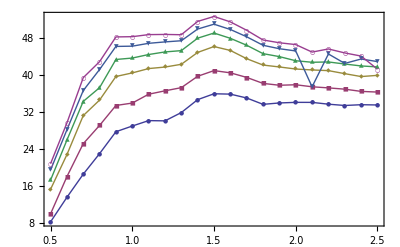
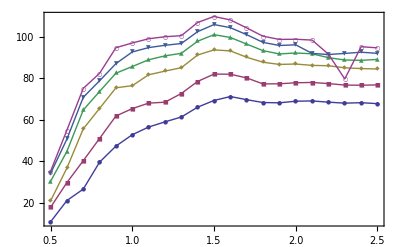
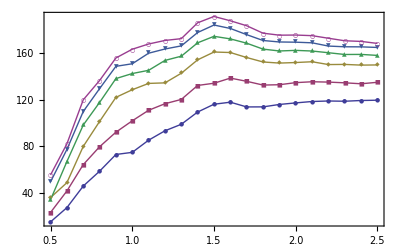

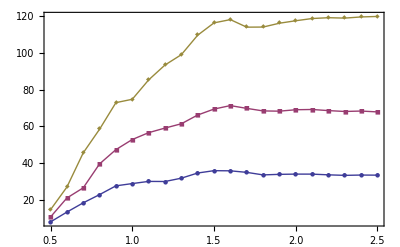
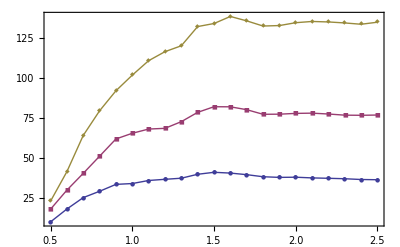
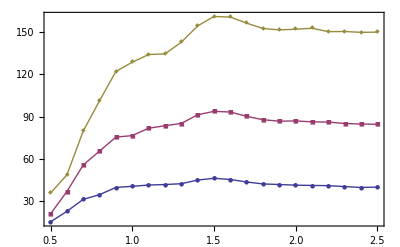
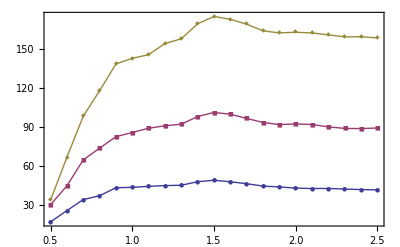
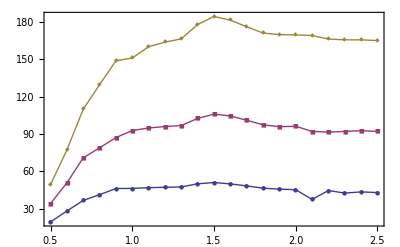

```mathematica
g1=With[{Vrange=({15,20,25}mm)^3,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]},{rr,{2,4,8,12,16,20}ohms},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
]
,{vv,Vrange}]
]
g2=With[{Rrange={2,4,8,12,16,20}ohms,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]},{vv,({15,20,25}mm)^3},{dd,Drange}],
Joined->True,PlotRange->Full,PlotMarkers->{Automatic,6},Axes->False,Frame->True
]
,{rr,Rrange}]
]
```

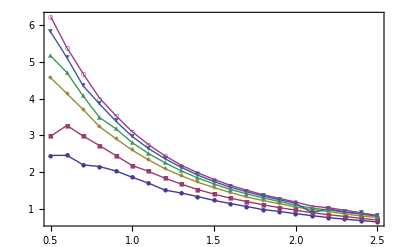
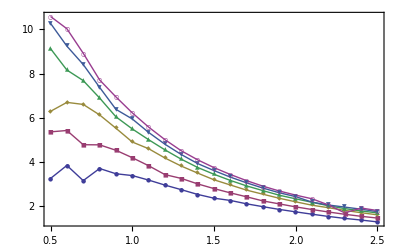
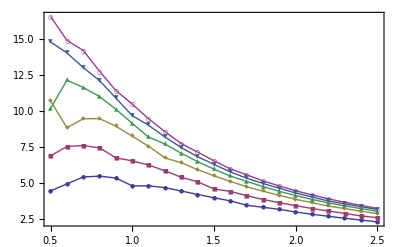

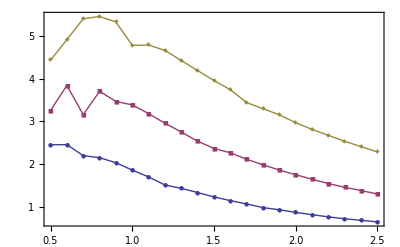
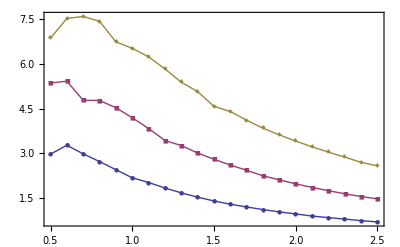
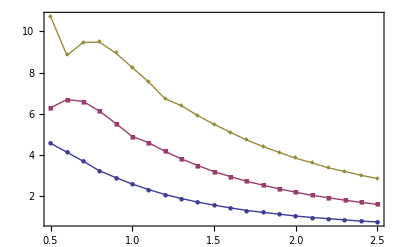
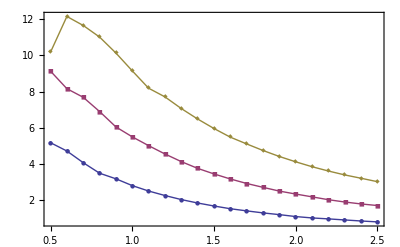
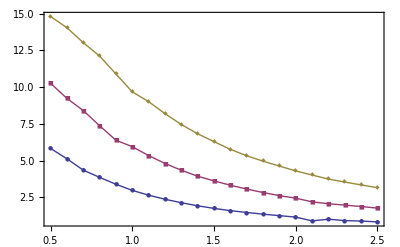

```mathematica
g1=With[{Vrange=({15,20,25}mm)^3,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]/CurrentFromDiam[dd]},{rr,{2,4,8,12,16,20}ohms},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
]
,{vv,Vrange}]
]
g2=With[{Rrange={2,4,8,12,16,20}ohms,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]/CurrentFromDiam[dd]},{vv,({15,20,25}mm)^3},{dd,Drange}],
Joined->True,PlotRange->Full,PlotMarkers->{Automatic,6},Axes->False,Frame->True
]
,{rr,Rrange}]
]
```

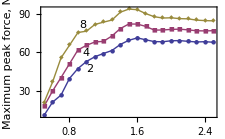

```mathematica
annot[s_,t_]:=PSfrag[s,TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{"<>t<>"}"]
forcemaxPlot=With[{vv=(20mm)^3,Drange=Range[5,25,1]/10 mm,Rrange={2,4,8}ohms},
Show[{
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]},{rr,Rrange},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
],
Graphics@{
Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{1,-6+First@ratiomax[1mm,#,vv]},{-1,0}]&@Rrange[[1]],
Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{1,-6+First@ratiomax[1mm,#,vv]}]&@Rrange[[2]],
Text[annot[ToString[#],"$\\resistanceCoil=\\SI{"<>ToString[#]<>"}{\\ohm}$"],{1,5+First@ratiomax[1mm,#,vv]},{1,0}]&@Rrange[[3]]}
},FrameLabel->{"Wire diameter, mm","Maximum peak force, N"},ImageSize->8 72/2.54]
]
```

```mathematica
PSfragExport["fig/magcoil-ratiomax",forcemaxPlot,RenumberTags->False]
```

{fig/magcoil-ratiomax,fig/magcoil-ratiomax-psfrag.eps,fig/magcoil-ratiomax-psfrag.tex}

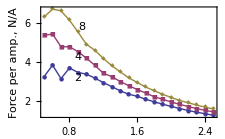

```mathematica
annot[s_,t_]:=PSfrag[s,TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{"<>t<>"}"]
normMaxForcePlot=With[{vv=(20mm)^3,Drange=Range[5,25,1]/10 mm,Rrange={2,4,8}ohms,ll=0.8mm},
Show[{
ListPlot[
Table[{dd/mm,First@ratiomax[dd,rr,vv]/CurrentFromDiam[dd]},{rr,Rrange},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
],
Graphics@{
Text[
annot[ToString[#1],"\\SI{"<>ToString[#1]<>"}{\\ohm}"],
{#2/mm,First@ratiomax[#2,#1,vv]/CurrentFromDiam[#2]},{0,1.5}]&[Rrange[[1]],0.9mm],
Text[
annot[ToString[#1],"\\SI{"<>ToString[#1]<>"}{\\ohm}"],
{#2/mm,First@ratiomax[#2,#1,vv]/CurrentFromDiam[#2]},{0,1.5}]&[Rrange[[2]],0.9mm],
Text[
annot[ToString[#1],"$\\resistanceCoil=\\SI{"<>ToString[#1]<>"}{\\ohm}$"],
{#2/mm,First@ratiomax[#2,#1,vv]/CurrentFromDiam[#2]},{-1,-1}]&[Rrange[[3]],0.9mm]}
},FrameLabel->{"Wire diameter, mm","Force per amp., N/A"},ImageSize->8 72/2.54]
]
```

```mathematica
PSfragExport["fig/magcoil-ratiomax-norm",normMaxForcePlot,RenumberTags->False]
```

{fig/magcoil-ratiomax-norm,fig/magcoil-ratiomax-norm-psfrag.eps,fig/magcoil-ratiomax-norm-psfrag.tex}

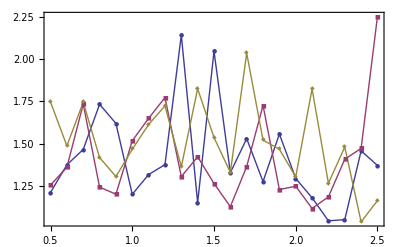
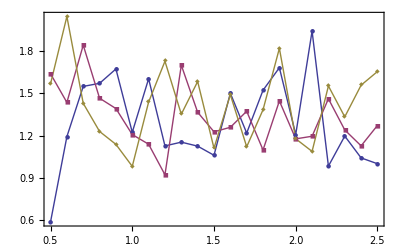
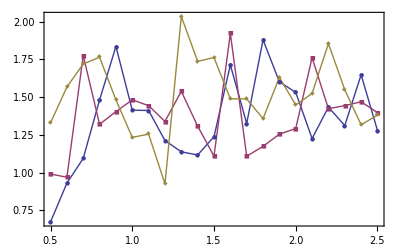

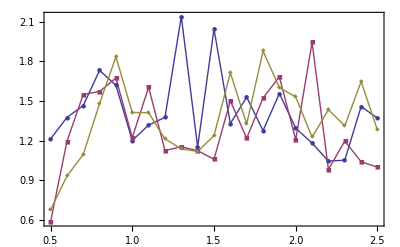
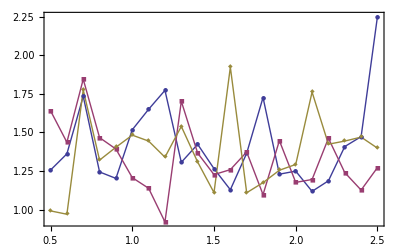
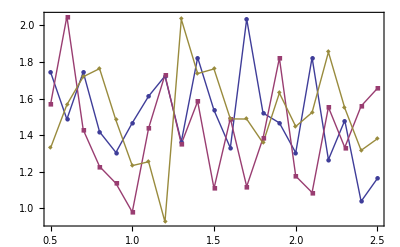

```mathematica
With[{Vrange=({15,20,25}mm)^3,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,a//.Last@ratiomax[dd,rr,vv]},{rr,{2,4,8}ohms},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
]
,{vv,Vrange}]
]
With[{Rrange={2,4,8}ohms,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,a//.Last@ratiomax[dd,rr,vv]},{vv,({15,20,25}mm)^3},{dd,Drange}],
Joined->True,PlotRange->Full,PlotMarkers->{Automatic,6},Axes->False,Frame->True
]
,{rr,Rrange}]
]
```

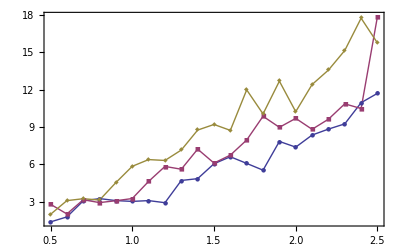
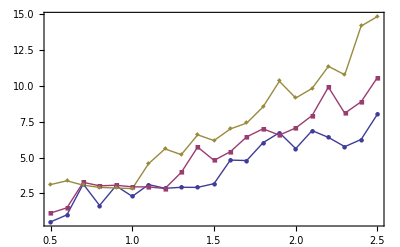
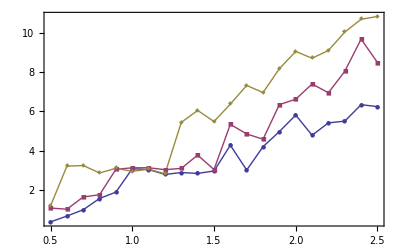

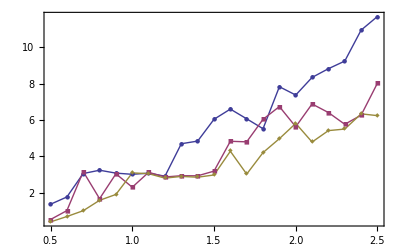
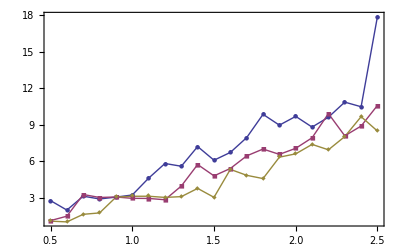
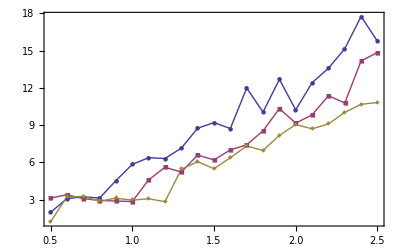

```mathematica
With[{Vrange=({15,20,25}mm)^3,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,b//.Last@ratiomax[dd,rr,vv]},{rr,{2,4,8}ohms},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
]
,{vv,Vrange}]
]
With[{Rrange={2,4,8}ohms,Drange=Range[5,25,1]/10 mm},
Table[
ListPlot[
Table[{dd/mm,b//.Last@ratiomax[dd,rr,vv]},{vv,({15,20,25}mm)^3},{dd,Drange}],
Joined->True,PlotRange->Full,PlotMarkers->{Automatic,6},Axes->False,Frame->True
]
,{rr,Rrange}]
]
```

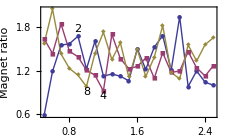

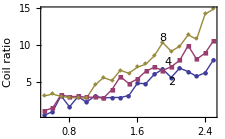

```mathematica
annot[s_,t_]:=PSfrag[s,TeXCommand->"\\fboxsep=1pt\\footnotesize\\colorbox{white}{"<>t<>"}"]
magRatioPlot=With[{vv=(20mm)^3,Drange=Range[5,25,1]/10 mm,Rrange={2,4,8}ohms},
Show[{
ListPlot[
Table[{dd/mm,a//.Last@ratiomax[dd,rr,vv]},{rr,Rrange},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
],
Graphics@Text[annot[ToString[#],"$\\resistanceCoil=\\SI{"<>ToString[#]<>"}{\\ohm}$"],{0.9,0.1+(a//.Last@ratiomax[0.9mm,#,vv])}]&[2],
Graphics@Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{1.2,(a//.Last@ratiomax[1.2mm,#,vv])},{0,1}]&[4],
Graphics@Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{1,(a//.Last@ratiomax[1mm,#,vv])},{0,1}]&[8]
},FrameLabel->{"Wire diameter, mm",PSfrag["Magnet ratio",TeXCommand->"Magnet ratio $\\ratioMag$"]},ImageSize->8 72/2.54]
]
coilRatioPlot=With[{vv=(20mm)^3,Drange=Range[5,25,1]/10 mm,Rrange={2,4,8}ohms},
Show[{
ListPlot[
Table[{dd/mm,b//.Last@ratiomax[dd,rr,vv]},{rr,Rrange},{dd,Drange}],
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True
],
Graphics@Text[annot[ToString[#],"$\\resistanceCoil=\\SI{"<>ToString[#]<>"}{\\ohm}$"],{2,(b//.Last@ratiomax[2mm,#,vv])},{0,1.5}]&[2],
Graphics@Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{2,(b//.Last@ratiomax[2mm,#,vv])},{1,-1}]&[4],
Graphics@Text[annot[ToString[#],"\\SI{"<>ToString[#]<>"}{\\ohm}"],{1.9,(b//.Last@ratiomax[1.9mm,#,vv])},{0,-1}]&[8]
},FrameLabel->{"Wire diameter, mm",PSfrag["Coil ratio",TeXCommand->"Coil ratio $\\ratioCoil$"]},ImageSize->8 72/2.54]
]
```

```mathematica
PSfragExport["fig/magcoil-ratiomax-a",magRatioPlot,RenumberTags->False];
```

```mathematica
PSfragExport["fig/magcoil-ratiomax-b",coilRatioPlot,RenumberTags->False];
```

```mathematica
Function[y,Function[x,f[x,y]][1]][2]
```

f[1,2]

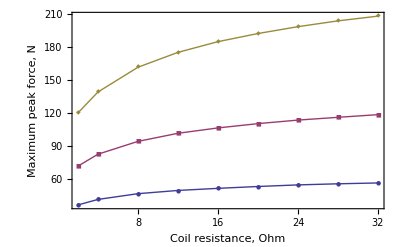

```mathematica
FnFirst[x_,y_]:=x
With[{Vrange=({15,20,25}mm)^3,Rrange={2,4,8,12,16,20,24,28,32}ohms,Drange=Range[5,25,1]/10 mm},
x=Table[{rr,Max[FnFirst@@@(Function[dd,ratiomax[dd,rr,vv]]/@Drange)]},{vv,Vrange},{rr,Rrange}];
g1=ListPlot[
x,
Joined->True,PlotMarkers->{Automatic,6},PlotRange->Full,Axes->False,Frame->True,FrameLabel->{"Coil resistance, Ohm","Maximum peak force, N"}
]
]
```

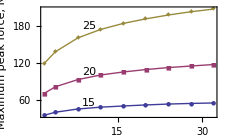

```mathematica
t1=Graphics@{Text[annot["15","$\\volMag=(\\SI{15}{mm})^3$"],{10,47},{0,-1}]};
t2=Graphics@{Text[annot["20","$(\\SI{20}{mm})^3$"],{10,98},{0,-1}]};
t3=Graphics@{Text[annot["25","$(\\SI{25}{mm})^3$"],{10,172},{0,-1}]};
coilResistancePlot=Show[{g1,t1,t2,t3},ImageSize->8 72/2.54]
```

```mathematica
PSfragExport["fig/magcoil-resistance",coilResistancePlot,RenumberTags->False];
```

```mathematica
With[{Drange=Range[5,25,1]/10 mm},
Max[FnFirst@@@(ratiomax[#,4ohms,(20mm)^3]&/@Drange)]
]
```

82.1104